```mathematica
data = "/Users/alexradcliffe/kcl/hyperbolic-python/clusterData100"
```

/Users/alexradcliffe/kcl/hyperbolic-python/clusterData100

```mathematica
lmaxs = Import[data<>"/lmaxs.json"]
```

{3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
positions = Flatten[Position[lmaxs,_?( Mod[#, 2]==1&&#<=90&)]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44}

```mathematica
lmaxs = lmaxs[[positions]]
```

{3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89}

```mathematica
S12 = 1.1540969443944852107791801492`29
```

1.1540969443944852107791801492

```mathematica
convert[x_] := ToExpression[x <>"`500"]
```

```mathematica
bounds = convert/@Import[data<>"/bounds.json"]
bounds = bounds[[positions]]
```

{1.151872038896995370187571057394491093205691239691934950686112774760855306889567752881784081488169195236619086983588865503254117420093160869011455645076599324013638448612151299852854861373490755669562399439288964411538401129895334181092099629240825440073581777938771853180822222233281250819010921715649569456842843482468554035188636909193881305607746977222488784402401675174758407858986505332521012401132002084281530859699926456804109640367881453525719219703134366435510565706643208372258372933530178,1.1540299131297621548314974915851539312663473136534969521889895153779397202983969163678158465453452354146415610968688489901854560095025989681271214390075680070475262737656593701694981398128788151063356408898979780851155992715408934768488728560812784638091126442698001543620926048300454167636764643758510477648836459782659719823417613473719452116020091042095289442523021140930319017379126995275244981663594145079145015602139941830396115749314097720324070914426677813734999042756726254152251094892209975,1.1540299131297621548314974915851539312663473136534969521889896094136887737583139068897112408457573520589336074731458429571194160923740240764073642723619749558572137082682365593909460087599817015196644639984796925518277117198060983749792295762958084100524117672082959839402540381156115293405105844370815908425508456995110336924035053895229564963394924250849345240202526477336519924924926140169678653938597370912976488326930205061130448164236578900666814519869907187126782155108265185794970927532401722,1.1540928962920960856193491532397031645984876352056836960627776201096717361717735710648382975477752587210114933763434098155964329941764106937776973676827622974888490966960333896638787773317390725625840545262935354114304003553269650498030489410716869146234503139829468466452440731766689866473261541950142156343611882943929607931678317185700578969234051449065755871851755679326981104679787931885372417229796076498694999106781010200647064191201540000764165773391610156256663123270888311022243155623803138,1.1540968196480896952137391471442681338133928708485496592083057456701108979945402077837235424902275814270080267826242992094193415259380705867720001296310083089053810934909964126470165120873000710258911068614226316391219720485553780149581736645895202631513796173688566373085694457120657317597881644442923298465751337501834165755143471512492616969065085628912524960605864882303216201548274040487618734450125869258724620170572166095729950759496678199204020418052535764255695526126634538723207521527308603,1.1540968196480896952137391471442681338133928708485496592083055173072357346935342669565572058148132804341924126830766386737214346196535317556433687162235745084134860330191386627952242920089392835262530838099989215263035991585647511726969326109295408482313810628641125709056002793885522500661836596430730509992811462812794561481212123364186696420559964620874196147410789182916719442690959636667635626028079057446147106347364367599960678773987514723374204691130041553703941490208364676991536560911574863,1.1540969351181001293814081394681830978396431359423413657669267248269781595295452753270389773635459185896094330585824940919370531175923658703930650885774558369132234729048649125940724433327714268206114964188531989953765188806033805214333992365322045668810563848184958401836356355791084327312057757234722208287761641499301533285127062022483182212090563106611430020891680556108402349003510578488965081400814459790171470890302831507210561977675603488358294585504419293846338773434268556149353571653816508,1.1540969351181001293814081394681830978396431359423413657669270205953873412735832747260537626573846756491589104139694143165765504141591089997304864306580769290328750406688768961293142742979477422566578343741992944205256481443916564846208404475973462734259247033543734387808057936222301213902504312193710039790401209292537978212744640567348851281143853223605054074349174329685960001345203538522039501757272159443669135791038699189475914580124651579765256985506915937020748549264312858924880264271759336,1.1540969428312073753381569524608301303370510718279453819377750461579323426677039677639187074832711661673944527340791032297273677626690562825299512078655914141784499558657271007702926854210856025247186256454519271503269542493566080014529582832797228598207881957258330396275375987941571427822230472492178127424863505405171213720006137415090565849336825932737484084958118611479695106730310722793992312124781642926915539853369563169908646280389660556708236234503086058819234071831471769300642421466231017,1.1540969442498077403973294222906153952940544837138245657435803028033814163803994901230139583087886098097289063403103724807565911524181831221589432558492860277826846579220451183256791723306160780287830532984447352441698624361641122733271699621882523872667820207329903672300950990533321078893154152118562980210725199726635506515596003136147133222931132518404837744717079674710362549676978977987926729348622439730737685907218048594818948850416272254156578933429158303467588700999802453406963033223678467,1.1540969442498077403973294222906153952940544837138245657435804811349357605891303550605918039733868626036155745968874024438681261030267239005386740330557183558712345133233430026926743672870303748251068511915711012364734691941842569004337839291523258401073973524807155910031772706051542229512725157513650274670501463297344771783175340629551726855968866910572953297487580686159484793516245995638765315439434011037190208598996130684537561940271420673322278574728765583796588086735384173644030716472065848,1.1540969442924988250428047416365791502867103695433427980204438552677459439860124625156752609577982977442129842148796760620301223015267296088709399073362626326438496831104694809318676863558285301862073353344918589609317526264076300395793059437746972429797979190707925409666400566188714946800519617911493434744929612918894396645446212274296154962894334622230143217890971532120612802845438450077255629379857694428127602694548673527794597182037627477372408095827354656222757061924966474175361459192994564,1.1540969442924988250428047416365791502867103695433427980204441711172162214672947491751005622880492070782491058496026655064086446514447375101425606955115510328918662763687773592761128719167618773923444640614276833405013129325710213753297892698494850641496908793504743015434249588457592330042474584191387236714732109525307394177741306597782748435538216205253914656860873108252831797587536278647761051752305509106225291210289015906991591922059890091403144508457104069486713835428549205226756378468437165,1.1540969443193095979002822768603600966613925182699127277482606391292588673088525432194366020151563631757131590593124748946934393548249717568569027078101260782813162487559116762297209568466547953851656866042207429497398423046777433596759680529124152935105026434130730278112672717423458098552444193382824434724644683609791653341646314020899138658198647383588723427914794992260114637444578094691258138915461991468436858745473146676172341102482271724097395423317981405449415449420229490885975030192360247,1.1540969443193095979002822768603600966613925182699127277482604551953626668674485080311477874531184455854422725802364055628087315883441874839674690878241784853971996091386254922722148885686460271629107298673632460953012816016269900115067446820703959711449107839783018798073551650677883168250017151457554445644919839522345865259953705224883118690581958966973998769602667588855116898347854467385229251876919296189335813937278205474872321608830125398723338735341209709853061564109102857034815772398934914,1.1540969443215443986359326120059813947773337451114808159780202728165531386748075506844276659514864122295354365634506311849925497694193694634301665775507814176540540429222068921691256801844903640552207845796846282934295347703490694216722576264797704744573539837918447113581906058288120320213989886859541386654756419524872128151504859115676489557791130948813442825402322937579041453966614820478839895610719895997024098230866487880219653839555316532589586130096799874210056650700499051974202978765342109,1.1540969443215877925940839179766300221087384497761094212950054390758372063790824070862069313135091345654614368674311408225388310206738904630766204220146143996358852905354438885192073179559364866285261939708848418918664115857598628518744414345371165147227109099823740197365418318115792179967009511957416518227821786491775345809138491806275635797518716527770956064715530852410562555283214197537097299097199896714075704709378401930013921251930045441209362219184259319537024276812910669918151561939870132,1.1540969443221336345095061916040980754602678446050866178576180841185284948272213379953079298427900775095405483540485992398652693795849525533464707039753442864830310489133581996647372253479043788270181265544203910306375185569160638542068522995190691261400938187213370300858150488418154891632526589296153773856411028711837285584216609655123927980562395265923147111543103138230934230087894421917835687923783869959182660357756902555517694391735515477991720453594321251155981696261262195249553703934634284,1.1540969443221355805087872231499256260588725068871483491487019470428736258396846470191098060433583335712300679722036163172358969978128048495591888195509776525500983387431896366309857951095884654075347920575559270405802435210671920977642589095265293130114472673607682798527466206662758617633025476218869615335647586742370180287388431661790806920371086927144257848422272915819014638847856348821460955011064193950125370933281800703620138156386188029784030193132084108702463752137352393638848924951735877,1.1540969443222475223477632150817884154037111047821824557875794071966383850751898607602945485671830047127773110142799082443752292370876474145502096476926361324667359075958276201219528134154532144094808600056925073289037270751184698044854126722813082788610301462536093696982804537547954647265552909087186088506097680212812603411373954249685869504575346353178363429460510519457351668295243086996905277468263056291157529654837388353684482786145717983318464276001961593145387091225532840408108483462822212,1.1540969443222475223477632150817884154037111047821824557875793862426785753745921746484623403482907299839390357237128559406182165823066747499558238242306320987046461816155120822635593267713367192219854167925423569038695971159012457665687697361059444691592615816050361918007258231810234425141154647947118020581029291531324722959369371803317669826775254112110403486447182920864866218052323417412396519704394002166620796627240029774871755876184242221659280344323892533708845533667206700262315604178473648,1.1540969443223105339033776350494440375985541102398146106233757327683473450300157565112335162220647619452623877407929830608117476451518338140233940966209626569649262789053746318038171496575223894906387351539111941313178248353694025813034388401923716508089981548199799463553913646305011247565164690487166961868965033009522700874202798066597308769381652569159849012210617813365578068526883544763505475450723958973641973397191785864025559224322435763900656055377703609287494929535786409128363582645426845,1.1540969443223745647003813311363856052824158366210403803376409498943078456785897155283152158634758604716601698335682382578531825783569402423092803941006489707331562377756851271036238193731946552824992130976952532740001165633317927332464683567987163146610467574966345638359651462196756616704486874537477730487104831073912382018949984997681774067450525409891707194368267039848710664319522981009937155507041789965007345786091769755830811361981161098116346471062707898331554783499915706161625779752200455,1.1540969443223746001149199068590037766536684521484925925329226537684483770727775683945001781303661327696436568839811972605699328370459534966672124284330320437284525635921352559773487625561981203477027508868021125217908107812319039938028118011100662278126331867833185701240132478774229904490024410559509418182623664753897620358772874052235837558566520797526671258924297367293515097252439107467962679202598851444338513486052852349663172231665230425527908615758948933093948003252852121506382904396957627,1.1540969443223967137004396459802450647385081680799898424894668829680491056250703506055929512199651480013013420606794546942677170047748334148415018245430361435574786192154092323188169537415689198475923385181731709249199671565551734619435839192973997944853050979163364354246438701719259747585805516417879612289847952915932646345077967196424943982401436928200577799294023003503565542955045758433306310270068588413182291885046192081694803621831351409472677397606473888801169316371560659580244347819995086,1.1540969443223969747799972437076711881057912472940913189695526898499423371710518768952743007817977986381877559475999772497300326117359107873371775203705340540071388344138827500095260577443351627501624664295879908828107746359157905114933019656588251478740502373762765891772319752174221999724894104326481684747855084754448332708741183188862713559879912179048415600963016311413301417253077153611424738954542123303917609400150270500200783518530665458091644644236203594413732969129856567444619418642833319,1.1540969443223989162731583940798417172432584307035645887888991558886206911102010319237713505377764310696717334392071312755034568867488660299390920946546107310545279385047103040399591026559648770433782183073673735650989526074151982552994734860772826867699689416513038956252700552865915687288709394565239144352115357146769437054725722461227784368348306406568705595680430910998171930744006151517533403957282458521663477415025618213488579720317921217904242457738098855809416697356733188295482768910377379,1.1540969443223989471326215415327752016270069696925922803276385785438684561941706602167644775511915570731622814938758588002766896883109554111250022950984146955088157008478623481892991050825296161926545700055908582374258706281768770835975583042167552293968104964528313606608850591440861277658667237516033936414786480731320631217886597508858138798260651961134861625915446009859506063590955013876617401726487543478984634606563756510161429394486632986137049386892185276466089390547396444534084216538625098,1.1540969443223996483485218882011782785582703587891721775636230149766291098043339718373981081514720287065912919402493491982349171141056356045128316136266687961116141566349024912981539731172846187118639698233243199004957037724735773418382519675457610808275532769484255588846601986489331426106625287602272137425644181259147597879169718484089975292846299694030004905079839229111498226549797675331943815989843020247014101912726317166901296578067443238553404938651774563222633808646812902662561562954831676,1.154096944322399780378521118301448519706639421530206910336034801145807664734868184554938710543758436067616493825640888321269724982649913973151838118812664021569057033571995780513839889552231541185475087301486945759237752463179425146463026565756530755263782470368937616631980916896048978085161996011590253101527710053419067039897477278465919767861853732943028603095297968380935005680514599131681602380328383448251697124040716649267495901006401440282543957021350983911749035317875379710100548539564539,1.1540969443223998166785442838342230127733731882703082144102574316623416161831318425113004768794015346483620758993702760364063862984069992164205271593284376152650664543800582339293423820835332840078041740425836216715469321578533451730989485795984106686351981407248203287206558529568875495219664137346542352404527240293927426663320159206458906358654172414961327315529431844747970453892843386800345094271234367220449911374646155764455922726064410242635264500944114737070297591538470696956024597331861932,1.1540969443223998166785442838342230127733731882703082144102573942758470017107563816161419929898884295721473638219018869020918625878029068545319172008757773837483667819009306580374798131497892646907598429058250125321827471939969263239509689453097956874202515783703437213576789335793360414376792391570701800026742480882354338851145729523919965312411421789587104579824310042671718128749488433107987200619021097352422892032044852821139278524962055545727242168514930833073572478168654875784626574324434883,1.1540969443223999269722220618702905271238563556813497074425115328912169365996356045355361871792725157095373298952166239369253138599963625788729200428385246751515215759823151047410504976979828935206876180495457413980265018500681935915277322280124673977281661811608453704085401969817479287622814403968696128777776513548513059736464075299487067900284263087721111557837562195637112593136668238718916874686517562464906542632545173978125028534982731427447621936790194791708061112438776419291710310678412109,1.1540969443223999664219704654045087561234864788095384421891655197193541728885823580103105790380878594522864134685762829826979728511530025350430890967386851892133180614193197997523138094793076036428446429335335982008696653077173979070337827707318468774700681716637284571577805383634980187378075829908934152798915474716790858704000126907851825475240148167764563469559719755920797965399006022451089150255792895199612669916054198065028455592219080094908553346550416136766506019743981981600068625195710179,1.1540969443223999863554297245647570873331022124503737270611005252050622538027077132737214550695496005121755936478674536607592484739112725279114279378805958090191472499183314934042073188968105387056533159478427041082071916427260451648991616236648416870001572416523389208588802726452794363116329121806258854690364515541484674784779111624699254600267852517374358766308614585406386729909793063044588293601007570037817986864200448735355647610184422705478748544888563386707257621668686776387192137393539165,1.1540969443224001082456440507467865625168265353423676165182275312441924764813444954593170452021392395954125506236620108194954949810325865493481105662119686353826760790845055421414817468641958205220338418422570897016060359027623401133616930131581709549278357465438873999418427699950086044846165897364987003716338455341522268923471933506137540420503320122531147832606770753653568616841359576013069069710220080605756127806448089933589946640361538373094882173868192020836130284710221476172121439206761423,1.1540969443224001301321183563925349388544854845958271554731462411222242818446191077079982677392833305520014880494516464159389910493695866334293954461733850318678071137687353839904399690242820590353037787979184532093515673760776757934021648855450030051091425323825781604897664824831833915392329591948800521498986666909154264872218326725247569221452978119902639782117676605494605148983210188836237978682615041756092999691413205154599722709685432299662959054905236081241111335959784918227680183161243472,1.1540969443224001909751706444847534531781147663797933484445942870617316681341248612645655741478042432045822606098498310633490493522741225169702182759083612717715489985879948017366673379488707492455857670539150861963575472607636743163953328437868139772037748858297430619827094018391785380376782177378164043657320594487043862496228503352766850176292642658126470483899429406910019811224715269368898390240694816854435112404986514247540746037522071875988020360238193694352354647351811282737887226164471078,1.1540969443224002149671936794432144945155243910898162211991434629583627290724982637819451383487880237929739270574285647393404346181165145631975889287464837994019125976381508128652076922591286324195047978123736637566312981011969473471710964671537916076221152812839666378688085139470406730644914496139801622837976606346637863459742569249628821010873116189037454977911837445899579302098536276194402662781593078867112890622168501633217867124586098383271967225216276450512271884070976080591128705668476704,1.1540969443224002203055375646556037712742901479839088764079141025679369524520583646551340863648049420889781072726315125890175097155962253120714670571106519365248184335269065030759667534268746680415941239417473179219261947278933887645369199305198298631964342585883331245431552561190086147331551687040541352141738446507852571076867527978613946056866423732550623093541006085597860619695610849727052856684116507265861760674834432287712861385154572491863311333932097204144013435696970557629254180905604694,1.1540969443224002541374679290330925154823071086826427371609783770771671540715590337769299254254051804329324234858312267357865624708014522607687855834244037130969072709210581155296999997322969646957820101796973762165951126766586321310471945500962796298729100235677111945912897263784654089749731073541377686361881809989621799002626436034384221800463809526109328703745189304848904658367247477672631412198086615587980585188681002053873056890132908642671024027786924864403835852952346646581720177138863656,1.1540969443224002541374679290330925154823071086826427371609783770771762093281916221410102225044380962560585217359763406777462148982020304559226032540151862419030895581883508327796248860834613293959392921739167817340754558228127167553022883362528349049359055251475184432961938954017505304196487296018571955826256519122638958467458439433663673468663463433646922718242243569097858489032196308561611602941279499205708629984962689238161950997519450635743269867512140371475492833649380603334891052177085202,1.1540969443224002763341672906101040583403813317451324350132178379863764084097538065185576103264778515564580412138188527131393704042122210469576879484099571510155142780394887150848453430497709611242486647446391316227703720041128411607968474369130241306998140062213154971252469491439684762886039035896605341887256473356609527507811505417578018011739384951376623689260708533502322455131169201873729840227172469544243187212722443863519031308148162994825811851070301900027953207397404821741087917959026164,1.1540969443224002804759638473450086221252278285633342003186162317931753901392189863712460524763034965061229139776568841083874522127106326713306973193825059127247452525694878280464190128427457827687373638022992048487441382359351393567375484177988640760269153074057673899040317405145914565847293148928763416012690173214571390958564428492148483213112504286288397384579042825021924009668455024826743946765043896689262979148663444901758979285973916777772423293716291507904731116028396265950586434551580202,1.1540969740642544873632423105238330250261993340979456289361278845202851592795512443708188642531267366550793606813464056057273160082611080664497926923890389551415952025010902772139128702268062089614336642612202054896511716790040873247766558021488563247649196881112681291192072215763431867028404569925267157254276963158531958302894823068039322229752932923965494975972955323701887852599424580298628185719869289940775639941061091456731471689879204601966903095472144770545665944930117839043446086894648427,1.1540969443225121890758872158437549271076745503124699061700933845932564364077382966644791756876514721456348951687948044622250975598923254416578533853964115864891518942081403005711577506783877731430222116131141864390589910445658416445918480728629376944393776414143825616651018966352135551347195743488509094468201272365931432651414742581542179985695636290294969441425518641757988437902161578504022597371683029113999263756185896174135109664744098912871499181499831832434044362725209465881230326885472458,81.932055445597656713191008451643563322291616043661099766351999820997155263702397887169344201195253705648865491483876926803833610650776573220040298125361535861862851398217100401206234411882766768613620112510994814342822137233157170138087219630728327521852798905790570325370206209693617905894349169557533609468985090431140520338901849047558892444388266534972183288224573303719916989536059086089093244551084354793326816316752313002447149843024942732734936541810626941143966962600174044253424629409025533,81.729254397815870577224575869666605230110388191450487004884857171830223466130016593880630993292314589567688748329633669233316706814149049977719692621849705280429148121460175354932520173209416954671551466116944641160918011856140991263392962984753433115525937252947788760086946544876314229424911460480293228463884055066693552979123161071593189488581006450515893572335672326125361612659185465913468348466576911770960080696460707889996974393019748965790123172346321977011084483687354805173319781663390084,0.4967208604179099511885428514433860182900101785786959205926957136093647826917327553614305575570823278119031744503898762020678888541669417713941412027749016190405454001119785231370328156927915847190469729785080381374033673476415026248939962499385635862078974534692582636464287551604766942965150203234599565558661973189348142598451741157004739849581202470154291555816723583770104349303071478458501775489629761340349255370067010462490286337549262187699161856635724182480859293271809155136781149568662729}

{1.151872038896995370187571057394491093205691239691934950686112774760855306889567752881784081488169195236619086983588865503254117420093160869011455645076599324013638448612151299852854861373490755669562399439288964411538401129895334181092099629240825440073581777938771853180822222233281250819010921715649569456842843482468554035188636909193881305607746977222488784402401675174758407858986505332521012401132002084281530859699926456804109640367881453525719219703134366435510565706643208372258372933530178,1.1540299131297621548314974915851539312663473136534969521889895153779397202983969163678158465453452354146415610968688489901854560095025989681271214390075680070475262737656593701694981398128788151063356408898979780851155992715408934768488728560812784638091126442698001543620926048300454167636764643758510477648836459782659719823417613473719452116020091042095289442523021140930319017379126995275244981663594145079145015602139941830396115749314097720324070914426677813734999042756726254152251094892209975,1.1540299131297621548314974915851539312663473136534969521889896094136887737583139068897112408457573520589336074731458429571194160923740240764073642723619749558572137082682365593909460087599817015196644639984796925518277117198060983749792295762958084100524117672082959839402540381156115293405105844370815908425508456995110336924035053895229564963394924250849345240202526477336519924924926140169678653938597370912976488326930205061130448164236578900666814519869907187126782155108265185794970927532401722,1.1540928962920960856193491532397031645984876352056836960627776201096717361717735710648382975477752587210114933763434098155964329941764106937776973676827622974888490966960333896638787773317390725625840545262935354114304003553269650498030489410716869146234503139829468466452440731766689866473261541950142156343611882943929607931678317185700578969234051449065755871851755679326981104679787931885372417229796076498694999106781010200647064191201540000764165773391610156256663123270888311022243155623803138,1.1540968196480896952137391471442681338133928708485496592083057456701108979945402077837235424902275814270080267826242992094193415259380705867720001296310083089053810934909964126470165120873000710258911068614226316391219720485553780149581736645895202631513796173688566373085694457120657317597881644442923298465751337501834165755143471512492616969065085628912524960605864882303216201548274040487618734450125869258724620170572166095729950759496678199204020418052535764255695526126634538723207521527308603,1.1540968196480896952137391471442681338133928708485496592083055173072357346935342669565572058148132804341924126830766386737214346196535317556433687162235745084134860330191386627952242920089392835262530838099989215263035991585647511726969326109295408482313810628641125709056002793885522500661836596430730509992811462812794561481212123364186696420559964620874196147410789182916719442690959636667635626028079057446147106347364367599960678773987514723374204691130041553703941490208364676991536560911574863,1.1540969351181001293814081394681830978396431359423413657669267248269781595295452753270389773635459185896094330585824940919370531175923658703930650885774558369132234729048649125940724433327714268206114964188531989953765188806033805214333992365322045668810563848184958401836356355791084327312057757234722208287761641499301533285127062022483182212090563106611430020891680556108402349003510578488965081400814459790171470890302831507210561977675603488358294585504419293846338773434268556149353571653816508,1.1540969351181001293814081394681830978396431359423413657669270205953873412735832747260537626573846756491589104139694143165765504141591089997304864306580769290328750406688768961293142742979477422566578343741992944205256481443916564846208404475973462734259247033543734387808057936222301213902504312193710039790401209292537978212744640567348851281143853223605054074349174329685960001345203538522039501757272159443669135791038699189475914580124651579765256985506915937020748549264312858924880264271759336,1.1540969428312073753381569524608301303370510718279453819377750461579323426677039677639187074832711661673944527340791032297273677626690562825299512078655914141784499558657271007702926854210856025247186256454519271503269542493566080014529582832797228598207881957258330396275375987941571427822230472492178127424863505405171213720006137415090565849336825932737484084958118611479695106730310722793992312124781642926915539853369563169908646280389660556708236234503086058819234071831471769300642421466231017,1.1540969442498077403973294222906153952940544837138245657435803028033814163803994901230139583087886098097289063403103724807565911524181831221589432558492860277826846579220451183256791723306160780287830532984447352441698624361641122733271699621882523872667820207329903672300950990533321078893154152118562980210725199726635506515596003136147133222931132518404837744717079674710362549676978977987926729348622439730737685907218048594818948850416272254156578933429158303467588700999802453406963033223678467,1.1540969442498077403973294222906153952940544837138245657435804811349357605891303550605918039733868626036155745968874024438681261030267239005386740330557183558712345133233430026926743672870303748251068511915711012364734691941842569004337839291523258401073973524807155910031772706051542229512725157513650274670501463297344771783175340629551726855968866910572953297487580686159484793516245995638765315439434011037190208598996130684537561940271420673322278574728765583796588086735384173644030716472065848,1.1540969442924988250428047416365791502867103695433427980204438552677459439860124625156752609577982977442129842148796760620301223015267296088709399073362626326438496831104694809318676863558285301862073353344918589609317526264076300395793059437746972429797979190707925409666400566188714946800519617911493434744929612918894396645446212274296154962894334622230143217890971532120612802845438450077255629379857694428127602694548673527794597182037627477372408095827354656222757061924966474175361459192994564,1.1540969442924988250428047416365791502867103695433427980204441711172162214672947491751005622880492070782491058496026655064086446514447375101425606955115510328918662763687773592761128719167618773923444640614276833405013129325710213753297892698494850641496908793504743015434249588457592330042474584191387236714732109525307394177741306597782748435538216205253914656860873108252831797587536278647761051752305509106225291210289015906991591922059890091403144508457104069486713835428549205226756378468437165,1.1540969443193095979002822768603600966613925182699127277482606391292588673088525432194366020151563631757131590593124748946934393548249717568569027078101260782813162487559116762297209568466547953851656866042207429497398423046777433596759680529124152935105026434130730278112672717423458098552444193382824434724644683609791653341646314020899138658198647383588723427914794992260114637444578094691258138915461991468436858745473146676172341102482271724097395423317981405449415449420229490885975030192360247,1.1540969443193095979002822768603600966613925182699127277482604551953626668674485080311477874531184455854422725802364055628087315883441874839674690878241784853971996091386254922722148885686460271629107298673632460953012816016269900115067446820703959711449107839783018798073551650677883168250017151457554445644919839522345865259953705224883118690581958966973998769602667588855116898347854467385229251876919296189335813937278205474872321608830125398723338735341209709853061564109102857034815772398934914,1.1540969443215443986359326120059813947773337451114808159780202728165531386748075506844276659514864122295354365634506311849925497694193694634301665775507814176540540429222068921691256801844903640552207845796846282934295347703490694216722576264797704744573539837918447113581906058288120320213989886859541386654756419524872128151504859115676489557791130948813442825402322937579041453966614820478839895610719895997024098230866487880219653839555316532589586130096799874210056650700499051974202978765342109,1.1540969443215877925940839179766300221087384497761094212950054390758372063790824070862069313135091345654614368674311408225388310206738904630766204220146143996358852905354438885192073179559364866285261939708848418918664115857598628518744414345371165147227109099823740197365418318115792179967009511957416518227821786491775345809138491806275635797518716527770956064715530852410562555283214197537097299097199896714075704709378401930013921251930045441209362219184259319537024276812910669918151561939870132,1.1540969443221336345095061916040980754602678446050866178576180841185284948272213379953079298427900775095405483540485992398652693795849525533464707039753442864830310489133581996647372253479043788270181265544203910306375185569160638542068522995190691261400938187213370300858150488418154891632526589296153773856411028711837285584216609655123927980562395265923147111543103138230934230087894421917835687923783869959182660357756902555517694391735515477991720453594321251155981696261262195249553703934634284,1.1540969443221355805087872231499256260588725068871483491487019470428736258396846470191098060433583335712300679722036163172358969978128048495591888195509776525500983387431896366309857951095884654075347920575559270405802435210671920977642589095265293130114472673607682798527466206662758617633025476218869615335647586742370180287388431661790806920371086927144257848422272915819014638847856348821460955011064193950125370933281800703620138156386188029784030193132084108702463752137352393638848924951735877,1.1540969443222475223477632150817884154037111047821824557875794071966383850751898607602945485671830047127773110142799082443752292370876474145502096476926361324667359075958276201219528134154532144094808600056925073289037270751184698044854126722813082788610301462536093696982804537547954647265552909087186088506097680212812603411373954249685869504575346353178363429460510519457351668295243086996905277468263056291157529654837388353684482786145717983318464276001961593145387091225532840408108483462822212,1.1540969443222475223477632150817884154037111047821824557875793862426785753745921746484623403482907299839390357237128559406182165823066747499558238242306320987046461816155120822635593267713367192219854167925423569038695971159012457665687697361059444691592615816050361918007258231810234425141154647947118020581029291531324722959369371803317669826775254112110403486447182920864866218052323417412396519704394002166620796627240029774871755876184242221659280344323892533708845533667206700262315604178473648,1.1540969443223105339033776350494440375985541102398146106233757327683473450300157565112335162220647619452623877407929830608117476451518338140233940966209626569649262789053746318038171496575223894906387351539111941313178248353694025813034388401923716508089981548199799463553913646305011247565164690487166961868965033009522700874202798066597308769381652569159849012210617813365578068526883544763505475450723958973641973397191785864025559224322435763900656055377703609287494929535786409128363582645426845,1.1540969443223745647003813311363856052824158366210403803376409498943078456785897155283152158634758604716601698335682382578531825783569402423092803941006489707331562377756851271036238193731946552824992130976952532740001165633317927332464683567987163146610467574966345638359651462196756616704486874537477730487104831073912382018949984997681774067450525409891707194368267039848710664319522981009937155507041789965007345786091769755830811361981161098116346471062707898331554783499915706161625779752200455,1.1540969443223746001149199068590037766536684521484925925329226537684483770727775683945001781303661327696436568839811972605699328370459534966672124284330320437284525635921352559773487625561981203477027508868021125217908107812319039938028118011100662278126331867833185701240132478774229904490024410559509418182623664753897620358772874052235837558566520797526671258924297367293515097252439107467962679202598851444338513486052852349663172231665230425527908615758948933093948003252852121506382904396957627,1.1540969443223967137004396459802450647385081680799898424894668829680491056250703506055929512199651480013013420606794546942677170047748334148415018245430361435574786192154092323188169537415689198475923385181731709249199671565551734619435839192973997944853050979163364354246438701719259747585805516417879612289847952915932646345077967196424943982401436928200577799294023003503565542955045758433306310270068588413182291885046192081694803621831351409472677397606473888801169316371560659580244347819995086,1.1540969443223969747799972437076711881057912472940913189695526898499423371710518768952743007817977986381877559475999772497300326117359107873371775203705340540071388344138827500095260577443351627501624664295879908828107746359157905114933019656588251478740502373762765891772319752174221999724894104326481684747855084754448332708741183188862713559879912179048415600963016311413301417253077153611424738954542123303917609400150270500200783518530665458091644644236203594413732969129856567444619418642833319,1.1540969443223989162731583940798417172432584307035645887888991558886206911102010319237713505377764310696717334392071312755034568867488660299390920946546107310545279385047103040399591026559648770433782183073673735650989526074151982552994734860772826867699689416513038956252700552865915687288709394565239144352115357146769437054725722461227784368348306406568705595680430910998171930744006151517533403957282458521663477415025618213488579720317921217904242457738098855809416697356733188295482768910377379,1.1540969443223989471326215415327752016270069696925922803276385785438684561941706602167644775511915570731622814938758588002766896883109554111250022950984146955088157008478623481892991050825296161926545700055908582374258706281768770835975583042167552293968104964528313606608850591440861277658667237516033936414786480731320631217886597508858138798260651961134861625915446009859506063590955013876617401726487543478984634606563756510161429394486632986137049386892185276466089390547396444534084216538625098,1.1540969443223996483485218882011782785582703587891721775636230149766291098043339718373981081514720287065912919402493491982349171141056356045128316136266687961116141566349024912981539731172846187118639698233243199004957037724735773418382519675457610808275532769484255588846601986489331426106625287602272137425644181259147597879169718484089975292846299694030004905079839229111498226549797675331943815989843020247014101912726317166901296578067443238553404938651774563222633808646812902662561562954831676,1.154096944322399780378521118301448519706639421530206910336034801145807664734868184554938710543758436067616493825640888321269724982649913973151838118812664021569057033571995780513839889552231541185475087301486945759237752463179425146463026565756530755263782470368937616631980916896048978085161996011590253101527710053419067039897477278465919767861853732943028603095297968380935005680514599131681602380328383448251697124040716649267495901006401440282543957021350983911749035317875379710100548539564539,1.1540969443223998166785442838342230127733731882703082144102574316623416161831318425113004768794015346483620758993702760364063862984069992164205271593284376152650664543800582339293423820835332840078041740425836216715469321578533451730989485795984106686351981407248203287206558529568875495219664137346542352404527240293927426663320159206458906358654172414961327315529431844747970453892843386800345094271234367220449911374646155764455922726064410242635264500944114737070297591538470696956024597331861932,1.1540969443223998166785442838342230127733731882703082144102573942758470017107563816161419929898884295721473638219018869020918625878029068545319172008757773837483667819009306580374798131497892646907598429058250125321827471939969263239509689453097956874202515783703437213576789335793360414376792391570701800026742480882354338851145729523919965312411421789587104579824310042671718128749488433107987200619021097352422892032044852821139278524962055545727242168514930833073572478168654875784626574324434883,1.1540969443223999269722220618702905271238563556813497074425115328912169365996356045355361871792725157095373298952166239369253138599963625788729200428385246751515215759823151047410504976979828935206876180495457413980265018500681935915277322280124673977281661811608453704085401969817479287622814403968696128777776513548513059736464075299487067900284263087721111557837562195637112593136668238718916874686517562464906542632545173978125028534982731427447621936790194791708061112438776419291710310678412109,1.1540969443223999664219704654045087561234864788095384421891655197193541728885823580103105790380878594522864134685762829826979728511530025350430890967386851892133180614193197997523138094793076036428446429335335982008696653077173979070337827707318468774700681716637284571577805383634980187378075829908934152798915474716790858704000126907851825475240148167764563469559719755920797965399006022451089150255792895199612669916054198065028455592219080094908553346550416136766506019743981981600068625195710179,1.1540969443223999863554297245647570873331022124503737270611005252050622538027077132737214550695496005121755936478674536607592484739112725279114279378805958090191472499183314934042073188968105387056533159478427041082071916427260451648991616236648416870001572416523389208588802726452794363116329121806258854690364515541484674784779111624699254600267852517374358766308614585406386729909793063044588293601007570037817986864200448735355647610184422705478748544888563386707257621668686776387192137393539165,1.1540969443224001082456440507467865625168265353423676165182275312441924764813444954593170452021392395954125506236620108194954949810325865493481105662119686353826760790845055421414817468641958205220338418422570897016060359027623401133616930131581709549278357465438873999418427699950086044846165897364987003716338455341522268923471933506137540420503320122531147832606770753653568616841359576013069069710220080605756127806448089933589946640361538373094882173868192020836130284710221476172121439206761423,1.1540969443224001301321183563925349388544854845958271554731462411222242818446191077079982677392833305520014880494516464159389910493695866334293954461733850318678071137687353839904399690242820590353037787979184532093515673760776757934021648855450030051091425323825781604897664824831833915392329591948800521498986666909154264872218326725247569221452978119902639782117676605494605148983210188836237978682615041756092999691413205154599722709685432299662959054905236081241111335959784918227680183161243472,1.1540969443224001909751706444847534531781147663797933484445942870617316681341248612645655741478042432045822606098498310633490493522741225169702182759083612717715489985879948017366673379488707492455857670539150861963575472607636743163953328437868139772037748858297430619827094018391785380376782177378164043657320594487043862496228503352766850176292642658126470483899429406910019811224715269368898390240694816854435112404986514247540746037522071875988020360238193694352354647351811282737887226164471078,1.1540969443224002149671936794432144945155243910898162211991434629583627290724982637819451383487880237929739270574285647393404346181165145631975889287464837994019125976381508128652076922591286324195047978123736637566312981011969473471710964671537916076221152812839666378688085139470406730644914496139801622837976606346637863459742569249628821010873116189037454977911837445899579302098536276194402662781593078867112890622168501633217867124586098383271967225216276450512271884070976080591128705668476704,1.1540969443224002203055375646556037712742901479839088764079141025679369524520583646551340863648049420889781072726315125890175097155962253120714670571106519365248184335269065030759667534268746680415941239417473179219261947278933887645369199305198298631964342585883331245431552561190086147331551687040541352141738446507852571076867527978613946056866423732550623093541006085597860619695610849727052856684116507265861760674834432287712861385154572491863311333932097204144013435696970557629254180905604694,1.1540969443224002541374679290330925154823071086826427371609783770771671540715590337769299254254051804329324234858312267357865624708014522607687855834244037130969072709210581155296999997322969646957820101796973762165951126766586321310471945500962796298729100235677111945912897263784654089749731073541377686361881809989621799002626436034384221800463809526109328703745189304848904658367247477672631412198086615587980585188681002053873056890132908642671024027786924864403835852952346646581720177138863656,1.1540969443224002541374679290330925154823071086826427371609783770771762093281916221410102225044380962560585217359763406777462148982020304559226032540151862419030895581883508327796248860834613293959392921739167817340754558228127167553022883362528349049359055251475184432961938954017505304196487296018571955826256519122638958467458439433663673468663463433646922718242243569097858489032196308561611602941279499205708629984962689238161950997519450635743269867512140371475492833649380603334891052177085202,1.1540969443224002763341672906101040583403813317451324350132178379863764084097538065185576103264778515564580412138188527131393704042122210469576879484099571510155142780394887150848453430497709611242486647446391316227703720041128411607968474369130241306998140062213154971252469491439684762886039035896605341887256473356609527507811505417578018011739384951376623689260708533502322455131169201873729840227172469544243187212722443863519031308148162994825811851070301900027953207397404821741087917959026164,1.1540969443224002804759638473450086221252278285633342003186162317931753901392189863712460524763034965061229139776568841083874522127106326713306973193825059127247452525694878280464190128427457827687373638022992048487441382359351393567375484177988640760269153074057673899040317405145914565847293148928763416012690173214571390958564428492148483213112504286288397384579042825021924009668455024826743946765043896689262979148663444901758979285973916777772423293716291507904731116028396265950586434551580202}

```mathematica
limit = 1.15409694433`500.
```

1.15409694433

```mathematica
deltas = limit-bounds
```

{0.002224905433004629812428942605508906794308760308065049313887225239144693110432247118215918511830804763380913016411134496745882579906839130988544354923400675986361551387848700147145138626509244330437600560711035588461598870104665818907900370759174559926418222061228146819177777766718749180989078284350430543157156517531445964811363090806118694392253022777511215597598324825241592141013494667478987598867997915718469140300073543195890359632118546474280780296865633564489434293356791627741627066469822,0.0000670312002378451685025084148460687336526863465030478110104846220602797016030836321841534546547645853584389031311510098145439904974010318728785609924319929524737262343406298305018601871211848936643591101020219148844007284591065231511271439187215361908873557301998456379073951699545832363235356241489522351163540217340280176582386526280547883979908957904710557476978859069680982620873004724755018336405854920854984397860058169603884250685902279675929085573322186265000957243273745847748905107790025,0.0000670312002378451685025084148460687336526863465030478110103905863112262416860931102887591542426479410663925268541570428805839076259759235926357276380250441427862917317634406090539912400182984803355360015203074481722882801939016250207704237041915899475882327917040160597459618843884706594894155629184091574491543004889663075964946104770435036605075749150654759797473522663480075075073859830321346061402629087023511673069794938869551835763421099333185480130092812873217844891734814205029072467598278,4.0480379039143806508467602968354015123647943163039372223798903282638282264289351617024522247412789885066236565901844035670058235893062223026323172377025111509033039666103361212226682609274374159454737064645885695996446730349501969510589283130853765496860170531533547559268233310133526738458049857843656388117056070392068321682814299421030765948550934244128148244320673018895320212068114627582770203923501305000893218989799352935808798459999235834226608389843743336876729111688977756844376196862×10^-6,1.2468191030478626085285573186618660712915145034079169425432988910200545979221627645750977241857299197321737570079058065847406192941322799987036899169109461890650900358735298348791269992897410889313857736836087802795144462198504182633541047973684862038263114336269143055428793426824021183555570767015342486624981658342448565284875073830309349143710874750393941351176967837984517259595123812655498741307412753798294278339042700492405033218007959795819474642357443044738733654612767924784726914×10^-7,1.24681910304786260852855731866186607129151450340791694482692764265306465733043442794185186719565807587316923361326278565380346468244356631283776425491586513966980861337204775707991060716473746916190001078473696400841435248827303067389070459151768618937135887429094399720611447749933816340356926949000718853718720543851878787663581330357944003537912580385258921081708328055730904036333236437397192094255385289365263563240003932122601248527662579530886995844629605850979163532300846343908842514×10^-7,9.2118998706185918605318169021603568640576586342330732751730218404704547246729610226364540814103905669414175059080629468824076341296069349114225441630867765270951350874059275566672285731793885035811468010046234811193966194785666007634677954331189436151815041598163643644208915672687942242765277791712238358500698466714872937977516817787909436893388569979108319443891597650996489421511034918599185540209828529109697168492789438022324396511641705414495580706153661226565731443850646428346183492×10^-9,9.2118998706185918605318169021603568640576586342330729794046126587264167252739462373426153243508410895860305856834234495858408910002695135693419230709671249593311231038706857257020522577433421656258007055794743518556083435153791595524026537265740752966456265612191942063777698786097495687806289960209598790707462021787255359432651148718856146776394945925650825670314039998654796461477960498242727840556330864208961300810524085419875348420234743014493084062979251450735687141075119735728240664×10^-9,1.498792624661843047539169869662948928172054618062224953842067657332296032236081292516728833832605547265920896770272632237330943717470048792134408585821550044134272899229707314578914397475281374354548072849673045750643391998547041716720277140179211804274166960372462401205842857217776952750782187257513649459482878627999386258490943415066317406726251591504188138852030489326968927720600768787521835707308446014663043683009135371961033944329176376549691394118076592816852823069935757853376898×10^-9,8.01922596026705777093846047059455162861754342564196971966185836196005098769860416912113901902710936596896275192434088475818168778410567441507139722173153420779548816743208276693839219712169467015552647558301375638358877266728300378117476127332179792670096327699049009466678921106845847881437019789274800273364493484403996863852866777068867481595162255282920325289637450323021022012073270651377560269262314092781951405181051149583727745843421066570841696532411299000197546593036966776321533×10^-11,8.01922596026705777093846047059455162861754342564195188650642394108696449394081960266131373963844254031125975561318738969732760994613259669442816441287654866766569973073256327129696251748931488084288987635265308058157430995662160708476741598926026475192844089968227293948457770487274842486349725329498536702655228216824659370448273144031133089427046702512419313840515206483754004361234684560565988962809791401003869315462438059728579326677721425271234416203411913264615826355969283527934152×10^-11,3.75011749571952583634208497132896304566572019795561447322540560139875374843247390422017022557870157851203239379698776984732703911290600926637373673561503168895305190681323136441714698137926646655081410390682473735923699604206940562253027570202020809292074590333599433811285053199480382088506565255070387081105603354553787725703845037105665377769856782109028467879387197154561549922744370620142305571872397305451326472205402817962372522627591904172645343777242938075033525824638540807005436×10^-11,3.75011749571952583634208497132896304566572019795558288827837785327052508248994377119507929217508941503973344935913553485552624898574393044884489671081337236312226407238871280832381226076555359385723166594986870674289786246702107301505149358503091206495256984565750411542407669957525415808612763285267890474692605822258693402217251564461783794746085343139126891747168202412463721352238948247694490893774708789710984093008408077940109908596855491542895930513286164571450794773243621531562835×10^-11,1.0690402099717723139639903338607481730087272251739360870741132691147456780563397984843636824286840940687525105306560645175028243143097292189873921718683751244088323770279043153345204614834313395779257050260157695322256640324031947087584706489497356586926972188732728257654190144755580661717556527535531639020834665835368597910086134180135261641127657208520500773988536255542190530874186108453800853156314125452685332382765889751772827590260457668201859455058455057977050911402496980763975×10^-11,1.0690402099717723139639903338607481730087272251739544804637333132551491968852212546881554414557727419763594437191268411655812516032530912175821514602800390861374507727785111431353972837089270132636753904698718398373009988493255317929604028855089216021698120192644834932211683174998284854244555435508016047765413474004629477511688130941804103302600123039733241114488310165214553261477074812308070381066418606272179452512767839116987460127666126465879029014693843589089714296518422760106509×10^-11,8.4556013640673879940186052226662548885191840219797271834468613251924493155723340485135877704645634365493688150074502305806305365698334224492185823459459570777931078308743198155096359447792154203153717065704652296509305783277423735202295255426460162081552886418093941711879679786010113140458613345243580475127871848495140884323510442208869051186557174597677062420958546033385179521160104389280104002975901769133512119780346160444683467410413869903200125789943349299500948025797021234657891×10^-12,8.4122074059160820233699778912615502238905787049945609241627936209175929137930686864908654345385631325688591774611689793261095369233795779853856003641147094645561114807926820440635133714738060291151581081335884142401371481255585654628834852772890900176259802634581681884207820032990488042583481772178213508224654190861508193724364202481283472229043935284469147589437444716785802462902700902800103285924295290621598069986078748069954558790637780815740680462975723187089330081848438060129868×10^-12,7.8663654904938083959019245397321553949133821423819158814715051727786620046920701572099224904594516459514007601347306204150474466535292960246557135169689510866418003352627746520956211729818734455796089693624814430839361457931477004809308738599061812786629699141849511581845108367473410703846226143588971288162714415783390344876072019437604734076852888456896861769065769912105578082164312076216130040817339642243097444482305608264484522008279546405678748844018303738737804750446296065365716×10^-12,7.8644194912127768500743739411274931128516508512980529571263741603153529808901939566416664287699320277963836827641030021871951504408111804490223474499016612568103633690142048904115345924652079424440729594197564789328079022357410904734706869885527326392317201472533793337241382366974523781130384664352413257629819712611568338209193079628913072855742151577727084180985361152143651178539044988935806049874629066718199296379861843613811970215969806867915891297536247862647606361151075048264123×10^-12,7.7524776522367849182115845962888952178175442124205928033616149248101392397054514328169952872226889857200917556247707629123525854497903523073638675332640924041723798780471865845467855905191399943074926710962729248815301955145873277186917211389698537463906303017195462452045352734447090912813911493902319787187396588626045750314130495424653646821636570539489480542648331704756913003094722531736943708842470345162611646315517213854282016681535723998038406854612908774467159591891516537177788×10^-12,7.7524776522367849182115845962888952178175442124206137573214246254078253515376596517092700160609642762871440593817834176933252500441761757693679012953538183844879177364406732286632807780145832074576430961304028840987542334312302638940555308407384183949638081992741768189765574858845352052881979418970708468675277040630628196682330173224745887889596513552817079135133781947676582587603480295605997833379203372759970225128244123815757778340719655676107466291154466332793299737684395821526352×10^-12,7.6894660966223649505559624014458897601853893766242672316526549699842434887664837779352380547376122592070169391882523548481661859766059033790373430350737210946253681961828503424776105093612648460888058686821751646305974186965611598076283491910018451800200536446086353694988752434835309512833038131034966990477299125797201933402691230618347430840150987789382186634421931473116455236494524549276041026358026602808214135974440775677564236099343944622296390712505070464213590871636417354573155×10^-12,7.6254352996186688636143947175841633789596196623590501056921543214102844716847841365241395283398301664317617421468174216430597576907196058993510292668437622243148728963761806268053447175007869023047467259998834366682072667535316432012836853389532425033654361640348537803243383295513125462522269512895168926087617981050015002318225932549474590108292805631732960151289335680477018990062844492958210034992654213908230244169188638018838901883653528937292101668445216500084293838374220247799545×10^-12,7.6253998850800931409962233463315478515074074670773462315516229272224316054998218696338672303563431160188027394300671629540465033327875715669679562715474364078647440226512374438018796522972491131978874782091892187680960061971881988899337721873668132166814298759867521225770095509975589440490581817376335246102379641227125947764162441433479202473328741075702632706484902747560892532037320797401148555661486513947147650336827768334769574472091384241051066906051996747147878493617095603042373×10^-12,7.6032862995603540197549352614918319200101575105331170319508943749296493944070487800348519986986579393205453057322829952251665851584981754569638564425213807845907676811830462584310801524076614818268290750800328434448265380564160807026002055146949020836635645753561298280740252414194483582120387710152047084067353654922032803575056017598563071799422200705976996496434457044954241566693689729931411586817708114953807918305196378168648590527322602393526111198830683628439340419755652180004914×10^-12,7.6030252200027562923288118942087527059086810304473101500576628289481231047256992182022013618122440524000227502699673882640892126628224796294659459928611655861172499904739422556648372498375335704120091171892253640842094885066980343411748521259497626237234108227680247825778000275105895673518315252144915245551667291258816811137286440120087820951584399036983688586698582746922846388575261045457876696082390599849729499799216481469334541908355355763796405586267030870143432555380581357166681×10^-12,7.6010837268416059201582827567415692964354112111008441113793088897989680762286494622235689303282665607928687244965431132511339700609079053453892689454720614952896959600408973440351229566217816926326264349010473925848017447005265139227173132300310583486961043747299447134084312711290605434760855647884642853230562945274277538772215631651693593431294404319569089001828069255993848482466596042717541478336522584974381786511420279682078782095757542261901144190583302643266811704517231089622621×10^-12,7.6010528673784584672247983729930303074077196723614214561315438058293397832355224488084429268377185061241411997233103116890445888749977049015853044911842991521376518107008949174703838073454299944091417625741293718231229164024416957832447706031895035471686393391149408559138722341332762483966063585213519268679368782113402491141861201739348038865138374084553990140493936409044986123382598273512456521015365393436243489838570605513367013862950613107814723533910609452603555465915783461374902×10^-12,7.6003516514781117988217214417296412108278224363769850233708901956660281626018918485279712934087080597506508017650828858943643954871683863733312038883858433650975087018460268827153812881360301766756800995042962275264226581617480324542389191724467230515744411153398013510668573893374712397727862574355818740852402120830281515910024707153700305969995094920160770888501773450202324668056184010156979752985898087273682833098703421932556761446595061348225436777366191353187097337438437045168324×10^-12,7.600219621478881698551480293360578469793089663965198854192335265131815445061289456241563932383506174359111678730275017350086026848161881187335978430942966428004219486160110447768458814524912698513054240762247536820574853536973434243469244736217529631062383368019083103951021914838003988409746898472289946580932960102522721534080232138146267056971396904702031619064994319485400868318397619671616551748302875959283350732504098993598559717456042978649016088250964682124620289899451460435461×10^-12,7.6001833214557161657769872266268117296917855897425683376583838168681574886995231205984653516379241006297239635936137015930007835794728406715623847349335456199417660706576179164667159921958259574163783284530678421466548269010514204015893313648018592751796712793441470431124504780335862653457647595472759706072573336679840793541093641345827585038672684470568155252029546107156613199654905728765632779550088625353844235544077273935589757364735499055885262929702408461529303043975402668138068×10^-12,7.6001833214557161657769872266268117296917855897426057241529982892436183838580070101115704278526361780981130979081374121970931454680827991242226162516332180990693419625201868502107353092401570941749874678172528060030736760490310546902043125797484216296562786423210664206639585623207608429298199973257519117645661148854270476080034687588578210412895420175689957328281871250511566892012799380978902647577107967955147178860721475037944454272757831485069166926427521831345124215373425675565117×10^-12,7.6000730277779381297094728761436443186502925574884671087830634003643954644638128207274842904626701047833760630746861400036374211270799571614753248484784240176848952589495023020171064793123819504542586019734981499318064084722677719875326022718338188391546295914598030182520712377185596031303871222223486451486940263535924700512932099715736912278888442162437804362887406863331761281083125313482437535093457367454826021874971465017268572552378063209805208291938887561223580708289689321587891×10^-12,7.6000335780295345954912438765135211904615578108344802806458271114176419896894209619121405477135865314237170173020271488469974649569109032613148107866819385806802002476861905206923963571553570664664017991303346922826020929662172292681531225299318283362715428422194616365019812621924170091065847201084525283209141295999873092148174524759851832235436530440280244079202034600993977548910849744207104800387330083945801934971544407780919905091446653449583863233493980256018018399931374804289821×10^-12,7.6000136445702754352429126668977875496262729388994747949377461972922867262785449304503994878244063521325463392407515260887274720885720621194041909808527500816685065957926811031894612943466840521572958917928083572739548351008383763351583129998427583476610791411197273547205636883670878193741145309635484458515325215220888375300745399732147482625641233691385414593613270090206936955411706398992429962182013135799551264644352389815577294521251455111436613292742378331313223612807862606460835×10^-12,7.5998917543559492532134374831734646576323834817724687558075235186555045406829547978607604045874493763379891805045050189674134506518894337880313646173239209154944578585182531358041794779661581577429102983939640972376598866383069868418290450721642534561126000581572300049913955153834102635012996283661544658477731076528066493862459579496679877468852167393229246346431383158640423986930930289779919394243872193551910066410053359638461626905117826131807979163869715289778523827878560793238577×10^-12,7.5998698678816436074650611455145154041728445268537588777757181553808922920017322607166694479985119505483535840610089506304133665706045538266149681321928862312646160095600309757179409646962212020815467906484326239223242065978351144549969948908574676174218395102335175168166084607670408051199478501013333090845735127781673274752430778547021880097360217882323394505394851016789811163762021317384958243907000308586794845400277290314567700337040945094763918758888664040215081772319816838756528×10^-12,7.5998090248293555152465468218852336202066515554057129382683318658751387354344258521957567954177393901501689366509506477258774830297817240916387282284510014120051982633326620511292507544142329460849138036424527392363256836046671562131860227962251141702569380172905981608214619623217822621835956342679405512956137503771496647233149823707357341873529516100570593089980188775284730631101609759305183145564887595013485752459253962477928124011979639761806305647645352648188717262112773835528922×10^-12,7.5997850328063205567855054844756089101837788008565370416372709275017362180548616512119762070260729425714352606595653818834854368024110712535162005980874023618491871347923077408713675804952021876263362433687018988030526528289035328462083923778847187160333621311914860529593269355085503860198377162023393653362136540257430750371178989126883810962545022088162554100420697901463723805597337218406921132887109377831498366782132875413901616728032774783723549487728115929023919408871294331523296×10^-12,7.5997796944624353443962287257098520160911235920858974320630475479416353448659136351950579110218927273684874109824902844037746879285329428893480634751815664730934969240332465731253319584058760582526820780738052721066112354630800694801701368035657414116668754568447438809913852668448312959458647858261553492147428923132472021386053943133576267449376906458993914402139380304389150272947143315883492734138239325165567712287138614845427508136688666067902795855986564303029442370745819094395306×10^-12,7.5997458625320709669074845176928913173572628390216229228328459284409662230700745745948195670675765141687732642134375291985477392312144165755962869030927290789418844703000002677030353042179898203026237834048873233413678689528054499037203701270899764322888054087102736215345910250268926458622313638118190010378200997373563965615778199536190473890671296254810695151095341632752522327368587801913384412019414811318997946126943109867091357328975972213075135596164147047653353418279822861136344×10^-12,7.5997458625320709669074845176928913173572628390216229228237906718083778589897774955619037439414782640236593222537851017979695440773967459848137580969104418116491672203751139165386706040607078260832182659245441771872832446977116637471650950640944748524815567038061045982494695803512703981428044173743480877361041532541560566336326531336536566353077281757756430902141510967803691438388397058720500794291370015037310761838049002480549364256730132487859628524507166350619396665108947822914798×10^-12,7.5997236658327093898959416596186682548675649867821620136235915902461934814423896735221484435419587861811472868606295957877789530423120515900428489844857219605112849151546569502290388757513352553608683772296279958871588392031525630869758693001859937786845028747530508560315237113960964103394658112743526643390472492188494582421981988260615048623376310739291466497677544868830798126270159772827530455756812787277556136480968691851837005174188148929698099972046792602595178258912082040973836×10^-12,7.5997195240361526549913778747721714366657996813837682068246098607810136287539475236965034938770860223431158916125477872893673286693026806174940872752547474305121719535809871572542172312626361977007951512558617640648606432624515822011359239730846925942326100959682594854085434152706851071236583987309826785428609041435571507851516786887495713711602615420957174978075990331544975173256053234956103310737020851336555098241020714026083222227576706283708492095268883971603734049413565448419798×10^-12}

```mathematica
changes = bounds[[2;;]]-bounds[[;;-2]]
```

{0.00215787423276678464392643419066283806065607396156200150287674061708441340882916348603176505717604017802247411327998348693133858940943809911566579393096868303388782515350807031664327843938805943677324145060901367357719814164555929575677322684045302373553086633102830118127038259676416594466554266020147830804080249579741794715312443817806390599426212698704015984990043891827349387892619419500348576522741242363297070051406772623550193456352831850668787173953341493798933856902941704296673655569082,9.40357490534599169905218953943004121166442920463762769939669339600828714251082802428333544069488096874345025771892214478689471028864133288231085817144667121124482652048981303567202145299462432991229384958295781614332855661125768341200612305430776671997212450617100617440421510112847374833208754055797679505336406200907545799144894433672275003225833831472724790263230734332414922481180342743605443229373391783112351538931642719832640191747×10^-62,0.0000629831623339307878516616545492333321403215521867438737880106959829624134596641751270567020179066620778859031975668584770169018023866173703330953207873416316353884277968302729327685717573710429195905278138428596026886355208666748238193647758785045710385467746508627049900350610574573068155697579326247918103425948819271007643263290471014005839127198216410631649229201990461179754861791715693763291198705585718510779850805139516616026964961100097351253521702969129880968162623125227272228091401416,3.9233559936095943899939045649692149052356428659631455281255604391618227666367188852449424523227059965334062808893938229085317616598929943027619482460114165319967949630229831377347555609984633070523351290962276915716932284129651551247235178333485279293033859097906633253725353967451124620102492781142122139454557904557823465154326792037999831034179846769088754109202976235096868486108602246317220329792760029621063791155895082886568295138198439854644660925607999032402855746227700964365903505464×10^-6,-2.28362875163301005940827166336675414300992815614099547660535697906906284538831128631413407433800491895060471857749851792220078360787499638023051423710112818372889990626842261241053659979414919998554504744066402969166323513481693604504801219278847293987468903960427393134814830592054850512100803832881319507569938649675885731440381998310842204681181257751382320779849576927198550916347582981572692249421055175403591826986173167096061573374×10^-61,1.15470010434167668992323914964026250265093791706558621207519742424836011008370481771548732638155417020375505855418215618497938834114749696372353881328499737439885726249798848151323832143294358412608854277469072919722038629348736466625602663718649675321954383269278035356190556182665022116080399169829495017868650697180391493865829648579153059848573723387348089137319168290631255094182132945537273540234402436454293846390724988320368808876498408989437437774014239728322590387915781701074224164×10^-7,2.957684091817440379993990147852938387570595494773553869202246394972965667431293374213420806210921196515677640119835352418309651763154360463379553460954251491292637882759631874412110651417065448683185358775985971701580431216886590446554958987831502639567793236444927617578544865669069053290116993624053457493773577557652341692960033074420356457699653497664900735867682265352602449048091406962400002496643174409775830044302775526692617942828×10^-61,7.7131072459567488129926470324974079358856040161708480255625450013941206930378649448258864905182355423201096889131508173485099472827994647772075144851455749151968502046409784111231378602680607912712526327298013061049649515168321178356823765863948634923714596008467318051719270213919726160298468087634462296112633235507261496847741714568192972709132430010608944281793735105385107184271952810367509483483246404062330863980432731700265008976942979248996170121798485522567158910375762157194471681×10^-9,1.418600365059172469829785264957003411885879183805805256645449073712695522359095250825517443642334453606231269251029223389749126839628992047983694613604234702056318017555386486909530475504064427652992808093842908186807504271874211678908529527445993825007157327602557500259174965107092367962638485278586169432146429279558986572105656737359430658566735365975896106323066744294666825519393441722384079680382214605384848542491030257002661169744834269892607224464835462916833068410632061175744745×10^-9,1.78331554344208730864937577845664598252793886668256577029963111534950608540778379730777206432328088549855401297884366995194956414296796323797893126365992303606758020144627106613966964073452840615331747725223773082171551822115061957100539508729445977626357070926526757933749340459363303773439216811555277050101144912224383926701765083858609081157130645252269177808208971861308985514841916569964129960728032899938573558172023706768324838738×10^-61,4.26910846454753193459637549926558858295182322768633741328101833968821074550834569844114351405974096179922736181619961985000057083322658742805442767726151697871264782391933190687981553611004841429207577244582834322233731391455220146223714028724005665900769499634627860137172717287794460397843160074428149621549624862270871644744428106925467711657189920403390845961128009329192454438490313940423683390937394095552542843257035241766206804050129521098589072426168975189582300531330742720928716×10^-11,3.158494702774812822866594253013302509093340361216347229894443785223499180079012716207881752884002480165932583078783442451855609333472061371287269358243795695603061633913357504833260747878211698929602796817605767849022268877383241954966279893801969802496606412997532295094323486593472643881583023771438969901576132218994742097828570505422372447814678097688515740342379196994740022262614030736412629749413263956773503582731051394919275442601×10^-61,2.68107728574775352237809463746821487265699297278164680120426458415577940443360397271071560974640532097098093882847947033802342467143420122985750453894499723871343169536080849298929179928212225427930596092385293721067219843461787830629302293608117640625987262678423128965865768509969609191437198009912574084484259163905007423116390222660431178334808771053921884007282839857041816043497087163156482362211567535184130769180749180422381632694250914860877335962701613991680285659218651723923082×10^-11,-1.83933896200441404035188288814562037917590270886479076069331884707766480784272889433619985947592884116639617286183957506068278008768222254956736857496854438560703050753348169223370842019322365591859434771148003912106674557493030242704192526998907972484408744578808169260879601601996761668841661472465831212740340499773909672362730602888703854269527910104480819494120130001949365214632537405668797677169559635388531112663385115925779342533×10^-61,2.234800735650335145621298115941226841568088229759817621190471807359042653279878498367966644093163983214225622183818181075181979462697489726602932256854433783581399896910791615844336892310054712321382198128253168722079410165512944409374503312443199813542831550835440761023715196397273540198694100983658000252626289155115389079337086720917198183944405579965534872392455561876035309361064373380059980768828429358828240534733223072519113386624739475559016435699508659139619493938720636640719×10^-12,4.33939581513059706486273314047046646286053169851662592840677042748564017792653620227223359260003039805096375462812512545209996464538444638329819818312476132369963500816377714461225733054093912002135984368768154107934302021838080573460402653569261905293083783512259827671859753019625097875131573065366966903217657633632690599146239727585578957513239313207914831521101316599377058257403486480000717051606478511914049794267412374728908619776089087459445326967626112411617943948583174528023×10^-14,5.458419154222736274680533515293948289771965626126450426912884481389309091009985292809429440791114866174584173264383589110620902698502819607298868471457583779143111455299073919678921984919325835355491387711069711562010023324108649819526114173829087389630103492732170302362711665517077338737255628589242220061939775078117848848292183043678738152191046827572285820371674804680224380738388826583973245106955648378500625503773139805470036782358234410061931618957419448351525331402141994764152×10^-13,1.945999281031545827550598604662282061731291083862924345131012463309023801876200568256061689519618155017077370627618227852296212718115575633366067067289829831436966248569761684086580516665503135536009942724964151128243557406610007460186871353448639431249766931571824460372600049888692271584147923655803053289470317182200666687893980869166122111073687916977758808040875996192690362526708728032399094271057552489814810244376465067255179230973953776285754648205587609019838929522101710159×10^-15,1.11941838975991931862789344838597895034106638877460153764759235505213741184742523824671141547243042076291927139332239274842564991020828141658479916637568852637983490967018305864749001946067948136580288323483554051277706721153762754778965849582878892841089845533833088519602963252743286831647317045009347044242312398552258789506258420425942603410558103823760363833702944738673817544432245719886234103215872155558765006434462975952995353443408286987748444292333908818044676925955851108634×10^-13,-2.0953959809700597686111832208218892274728838275290567052303757012654780972664594385823462004033762089725980315537858393486644116495187495443213150150425034129959217224037916642936175363809701768564648573177897554630573772022212439826114006806792506838868148788045200458244636819967780009224106795994301332759859248545024291966958450875776386905412453673302759735857881272690996147576165918393167806905943654155755832614014579287928434856×10^-62,6.30115556144199676556221948430054576321548357963465256687696554235818627711758737740319613233520170801271201935310628451590640675702723903305582602800972898625495402578228861856702686533183613688372274482277194681568147346691040864271816497365732149437545546655414494776822424010042540048941287935741478197977914833426263279638942606398457049445525763434892500711850474560127351108955746329956807021176769951756089153803348138193542241375711053811075578649395868579708866047978466953196×10^-14,6.4030797003696086941567683861726381225769714265217125960500648573959017081699641411098526397782092775255197041434933205106428285886297479686313768229958870310495299806669715672265791860477943784059142682291727962390151943029516606344663852048602676654617480573781589174536913932218405031076861813979806438968114474718693108446529806887284073185818215764922648313259579263943624643168005631783099136537238889998389180525213765872533421569041568500428904405985396412929703326219710677361×10^-14,3.54145385757226181713712526155274522121952817038741405313941878528661849622668902722979834870504129590027167502586890132543579320343323830729952963258164501288737249431830034650652035377891068592477906942179001112605563434443113499131515864292866840062880481016577473287785537536022031687695518833679985238339822889054554063491115995387634964064556030327444804432932916126458025523695557061479331167699961082593832360869684069327411562144696241034762393219752936415344757124644757172×10^-17,2.2113585519739121241288084839715931497249956544229199600728552292782211092773089599015231657685176698257433697784167728879918174289396110004099829026055623273976341468191185370799499889587631371058403129156375323269468140772118187333566672671911133017865300630622294502984309578110585837019410722428816203502598630509314418910642383491613067390654036972563621005044570260665096534363106746973696884377839899333973203163139016612098394476878184752495570722131311870853807386144342303746×10^-14,2.610795575977274261233672830792141014764800858068818932315459815262896813495618326506368864138869205225554623156069610773724956756958274979104496602151984735176907091040027662429025701279114148199578908074793606170495497180463614253533887451394599401537525881050454962252139088587908602072458007131838515686363663215992437769577478475250847837801668993307909735874298031395178118428684473534890735317515104078418505979896699314048618967246629729705612563652758295907864375070822838233×10^-16,1.941493161150372170529137467183409473269819346466038678353939149155028497049755978632431483977491607154025773424275012955242601914574284076677047389104090827554030433044911629714293215751877779382682288177971499407743806171520418457538895918704275027306448038080069169368756381529023875745960426027239232110434598453927236507080846839422752028999471741459958487051349092899790610866500274033521774586801487534771328779620178725575981259781350189526139568372822687662085086335026754406×10^-15,3.08594631474529334843837485389890276915387394226552477650839696282929931270134151260034905480546687275247732328015620893811859102004438039644542877623431520441493400024265647391492763516982234846723269180207616788282980848181394725426268415548015274650356150038574945590369957842950794792062671123584551194163160875047630354429912345554566156030235015098861334132846948862359083997769205084957321157191538138296672849674168711768232806929154086420656672693190663256238601447628247719×10^-17,7.012159003466684030769312633890965798972359844364327606536101633116206336306002804716334290104463734903979582274257946801933878293185282541006027984557870401431088548680347550025192093998177334616630698331442967002582406936633290058514307427804955941982237751395048470148447958050086238201010857700527826966661283120975231836494585647732895143279164393219251992162958842661455326414263355476768029467306162560656739867183580810252416355551759589286756544418099416458128477346416206578×10^-16,1.32029999230100270241148369062741034732772411786169178554930534212717540602392286407361025201885391539123034807868544278368639006505185995225457442876937093289215685916434946922473611117478162625858742048690705847804624774598210769674436229193420512057747320718247115835474499467251363039358963291927504307251980505430056922238577223763540028112587314045469785183025534831598487220781344081423550286932768084932577366243199657116427203463156173527589485654453194089443844392244081371×10^-16,3.63000231655327744930667337667401013040742226305165339514482636579563617663356430985807455820737293877151366613157570852432686890405157735936960094208080624534155024925313017428223290867410966759123091796946739200266359220138418799133714156703558827120886749360608385714368044177230639821389250139759736756264345386421799708680035635085531041284576452160938620397087697395483529070467950532737932940134238989271780963716000395839809824930730604897952807238359716899855019111936216543×10^-17,-3.7386494614472375460895158483889513105076214712077468389134314523710604092361888609958452660231516699672479127575891862568933744019317044331136758609139364184963856418849147979634288614981214946562354476607362976919377551508084287174577584055237778475941157308781217442968253894104624275062537422273570512180207625232514335495369235789365221326986802701934260130294331664420110235469690802233242918390399672511336981582117139802300742705×10^-62,1.10293677778036067514350483167411041493032254138615369934888879222919394194189384086137389966073314737034833451272193455724341002841962747291403154794081384446703570684548193628829927775143720728865843754656071267267576763282702671710307914602790501649050861263402411887324602201239799432875103403266615872088531834577556710258787284129813400697801325215296539446438717980561092967406749646511248365060050032115698575001002067588172037976827526395863448863427012154350708373635397723×10^-16,3.9449748403534218228999630123128188734746653986828137236288946753474774391858815343742749083573359659045772658991156639956170169053900160514061796485437004695011263311781324710122157024883987856802843163457649204315506050542719379479741901990502883086749240341381750089975526142594023802402113896116827779896753605160836475757495588508004345191172215756028368537226233778373217227556927533273470612728350902408690342705723634866746093140976022134505844490730520556230835831451729807×10^-17,1.9933459259160248331209615733640835284871935005485708080914125355263410876031461741059889180179291170678061275622758269992868338841141910619805829188499011693651893509417502935062808673014309105907337526335008647257865378852932994809530089069988610463701099734281781417573825329189732470189144904082469381608077898471684742912502770434960979529674889482948558876451078704059349914334521467483820531694814625067032719201796534261057019519833814724994075160192470479478712351219782899×10^-17,1.21890214326182029475183724322891993889457127006039130222678636782185595590132589639083236956975794557158736246507121314021436682628331372826363528829166174048737274427967385281816380525894414385593398844260036294948462531389493329267927678504891548479082962497349729168172983677555872814902597393980003759413869282188143828582023546760515678906629815616824718188693156651296848077610921251056793814094224764119823429903017711566761613362897962863412887266304153469978492930181322226×10^-16,2.1886474305645748376337658949253459538954918709878031805363274612248681222537144090956588937425789635596443496068337000084081284879961416396485131034684229841848958222160086238513269936955661363507745531473315335680040471872386832050181306785838690760547923712488174787054616369458381351778264821156763199594874639321911002880094965799737149194951090585184103653214185061282316890897239496115033687188496511522100977606932389392656807688103704406040498105124956344205555874395448205×10^-17,6.08430522880922185143236292817839661929714480459395073862895057535565673064085209126525807725603981846474100583029045358835408228297349762399037418848192594177462273689245886902102819882559966329870059798846859985229931679582418109720946323534471649014929429193559951464984452585429363522158333927577889597624010176627519280954839664538223830701781752801415414662241505080532660411558079775098342112713573309092941023327836639576325061305332957613111243311392026364510207043003227605×10^-17,2.39920230349584610413374096247100228727545491758966310609383734025173795642009837805883916664475787336759913852658423920462273706528381225276303635990501560111285403543102578831739190307584585775602737508404332730307757636233669776304183403954542235758860991121078621350268132318761637579180656011859594000963514065896861970834580473530910984494012408038989559490873821006825504272540898262012677778217181987385677121087064026507283946864978082756159917236719164797853241479504005626×10^-17,5.338343885212389276758765756894092655208770639609574223379560100873188948016016918296004180215202947849677075097479710748873878128364168137122905835888755690210759061167746035622089326129373654165294896626696441417365823463366038255574318977304366486674346742171967941668663719090073972930376184016121470761712495872898512504599330754351316811562916863969828131759707457353265019390252342839874887005266593065449499426056847410859134410871582075363174155162599447703812547523712799×10^-18,3.38319303643774887442080169606987338607530642745092302016195006691217958390606002383439543162131997141467690527552052269486973185263137517765720888373941516124537332463054222966541878862379500582946689179487652433665102746195764497666764757649793780700481344702594567942418179386500836334220143363481769227925758908055770275743597385793558705610204183219251044038671636627945578555513970108322118824513846569766160195504978336150807712693854827660259822417255376088952465996233258962×10^-17,9.0552566325883640802970790329158231260982501451139419596524274005781951538176705907825288061822872672927172499248863511643647001572819942194055174803431461540846242550937861565552750629955015798072487049041690232851214446756222477194269464374709133017159464832003399279451668199653907537594014497054264248953830664948830888980190743192883617728044796281687184288894107386541993072245839725215507071656980697033956753170875038221545×10^-69,2.2196699361577011542858074223062489697852239460909200199081562184377547387822039755300399519477842512035393155506010190591035084694394770909112424719851137882305220456966309631728309372570722349888694916181300124405494559100660189225763908481073797053829053053742217945868955173987803338606099995423397056904035306598391434454307592151772970097101846496440446396609897289331211823728589297033853455722775975462535708031062871235908254198355816152855246037374802421840619686578194096×10^-17,4.1417965567349045637848464968182017653053983938067989817294651798526884421498256449496648727638380313952480818084984116243730093709725487617092309745299991129615736697929748216444886990576600732259737662318222981959407009808858399453271013011844518927787847913706229802961254113032158074125433699857961863450752923074570465201373119334911773695318334291519601554537285822953014106537871427145019791935941001038239947977825753782946611442645989607876777908630991444209498516592554038×10^-18}

```mathematica
positionChanges = Flatten[Position[changes,_?( #>10^-40&)]]+1
```

{2,4,5,7,9,10,12,14,16,17,18,19,20,22,23,24,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,43,44}

```mathematica
changeswithChanges=changes[[positionChanges-1]]
```

{0.00215787423276678464392643419066283806065607396156200150287674061708441340882916348603176505717604017802247411327998348693133858940943809911566579393096868303388782515350807031664327843938805943677324145060901367357719814164555929575677322684045302373553086633102830118127038259676416594466554266020147830804080249579741794715312443817806390599426212698704015984990043891827349387892619419500348576522741242363297070051406772623550193456352831850668787173953341493798933856902941704296673655569082,0.0000629831623339307878516616545492333321403215521867438737880106959829624134596641751270567020179066620778859031975668584770169018023866173703330953207873416316353884277968302729327685717573710429195905278138428596026886355208666748238193647758785045710385467746508627049900350610574573068155697579326247918103425948819271007643263290471014005839127198216410631649229201990461179754861791715693763291198705585718510779850805139516616026964961100097351253521702969129880968162623125227272228091401416,3.9233559936095943899939045649692149052356428659631455281255604391618227666367188852449424523227059965334062808893938229085317616598929943027619482460114165319967949630229831377347555609984633070523351290962276915716932284129651551247235178333485279293033859097906633253725353967451124620102492781142122139454557904557823465154326792037999831034179846769088754109202976235096868486108602246317220329792760029621063791155895082886568295138198439854644660925607999032402855746227700964365903505464×10^-6,1.15470010434167668992323914964026250265093791706558621207519742424836011008370481771548732638155417020375505855418215618497938834114749696372353881328499737439885726249798848151323832143294358412608854277469072919722038629348736466625602663718649675321954383269278035356190556182665022116080399169829495017868650697180391493865829648579153059848573723387348089137319168290631255094182132945537273540234402436454293846390724988320368808876498408989437437774014239728322590387915781701074224164×10^-7,7.7131072459567488129926470324974079358856040161708480255625450013941206930378649448258864905182355423201096889131508173485099472827994647772075144851455749151968502046409784111231378602680607912712526327298013061049649515168321178356823765863948634923714596008467318051719270213919726160298468087634462296112633235507261496847741714568192972709132430010608944281793735105385107184271952810367509483483246404062330863980432731700265008976942979248996170121798485522567158910375762157194471681×10^-9,1.418600365059172469829785264957003411885879183805805256645449073712695522359095250825517443642334453606231269251029223389749126839628992047983694613604234702056318017555386486909530475504064427652992808093842908186807504271874211678908529527445993825007157327602557500259174965107092367962638485278586169432146429279558986572105656737359430658566735365975896106323066744294666825519393441722384079680382214605384848542491030257002661169744834269892607224464835462916833068410632061175744745×10^-9,4.26910846454753193459637549926558858295182322768633741328101833968821074550834569844114351405974096179922736181619961985000057083322658742805442767726151697871264782391933190687981553611004841429207577244582834322233731391455220146223714028724005665900769499634627860137172717287794460397843160074428149621549624862270871644744428106925467711657189920403390845961128009329192454438490313940423683390937394095552542843257035241766206804050129521098589072426168975189582300531330742720928716×10^-11,2.68107728574775352237809463746821487265699297278164680120426458415577940443360397271071560974640532097098093882847947033802342467143420122985750453894499723871343169536080849298929179928212225427930596092385293721067219843461787830629302293608117640625987262678423128965865768509969609191437198009912574084484259163905007423116390222660431178334808771053921884007282839857041816043497087163156482362211567535184130769180749180422381632694250914860877335962701613991680285659218651723923082×10^-11,2.234800735650335145621298115941226841568088229759817621190471807359042653279878498367966644093163983214225622183818181075181979462697489726602932256854433783581399896910791615844336892310054712321382198128253168722079410165512944409374503312443199813542831550835440761023715196397273540198694100983658000252626289155115389079337086720917198183944405579965534872392455561876035309361064373380059980768828429358828240534733223072519113386624739475559016435699508659139619493938720636640719×10^-12,4.33939581513059706486273314047046646286053169851662592840677042748564017792653620227223359260003039805096375462812512545209996464538444638329819818312476132369963500816377714461225733054093912002135984368768154107934302021838080573460402653569261905293083783512259827671859753019625097875131573065366966903217657633632690599146239727585578957513239313207914831521101316599377058257403486480000717051606478511914049794267412374728908619776089087459445326967626112411617943948583174528023×10^-14,5.458419154222736274680533515293948289771965626126450426912884481389309091009985292809429440791114866174584173264383589110620902698502819607298868471457583779143111455299073919678921984919325835355491387711069711562010023324108649819526114173829087389630103492732170302362711665517077338737255628589242220061939775078117848848292183043678738152191046827572285820371674804680224380738388826583973245106955648378500625503773139805470036782358234410061931618957419448351525331402141994764152×10^-13,1.945999281031545827550598604662282061731291083862924345131012463309023801876200568256061689519618155017077370627618227852296212718115575633366067067289829831436966248569761684086580516665503135536009942724964151128243557406610007460186871353448639431249766931571824460372600049888692271584147923655803053289470317182200666687893980869166122111073687916977758808040875996192690362526708728032399094271057552489814810244376465067255179230973953776285754648205587609019838929522101710159×10^-15,1.11941838975991931862789344838597895034106638877460153764759235505213741184742523824671141547243042076291927139332239274842564991020828141658479916637568852637983490967018305864749001946067948136580288323483554051277706721153762754778965849582878892841089845533833088519602963252743286831647317045009347044242312398552258789506258420425942603410558103823760363833702944738673817544432245719886234103215872155558765006434462975952995353443408286987748444292333908818044676925955851108634×10^-13,6.30115556144199676556221948430054576321548357963465256687696554235818627711758737740319613233520170801271201935310628451590640675702723903305582602800972898625495402578228861856702686533183613688372274482277194681568147346691040864271816497365732149437545546655414494776822424010042540048941287935741478197977914833426263279638942606398457049445525763434892500711850474560127351108955746329956807021176769951756089153803348138193542241375711053811075578649395868579708866047978466953196×10^-14,6.4030797003696086941567683861726381225769714265217125960500648573959017081699641411098526397782092775255197041434933205106428285886297479686313768229958870310495299806669715672265791860477943784059142682291727962390151943029516606344663852048602676654617480573781589174536913932218405031076861813979806438968114474718693108446529806887284073185818215764922648313259579263943624643168005631783099136537238889998389180525213765872533421569041568500428904405985396412929703326219710677361×10^-14,3.54145385757226181713712526155274522121952817038741405313941878528661849622668902722979834870504129590027167502586890132543579320343323830729952963258164501288737249431830034650652035377891068592477906942179001112605563434443113499131515864292866840062880481016577473287785537536022031687695518833679985238339822889054554063491115995387634964064556030327444804432932916126458025523695557061479331167699961082593832360869684069327411562144696241034762393219752936415344757124644757172×10^-17,2.2113585519739121241288084839715931497249956544229199600728552292782211092773089599015231657685176698257433697784167728879918174289396110004099829026055623273976341468191185370799499889587631371058403129156375323269468140772118187333566672671911133017865300630622294502984309578110585837019410722428816203502598630509314418910642383491613067390654036972563621005044570260665096534363106746973696884377839899333973203163139016612098394476878184752495570722131311870853807386144342303746×10^-14,2.610795575977274261233672830792141014764800858068818932315459815262896813495618326506368864138869205225554623156069610773724956756958274979104496602151984735176907091040027662429025701279114148199578908074793606170495497180463614253533887451394599401537525881050454962252139088587908602072458007131838515686363663215992437769577478475250847837801668993307909735874298031395178118428684473534890735317515104078418505979896699314048618967246629729705612563652758295907864375070822838233×10^-16,1.941493161150372170529137467183409473269819346466038678353939149155028497049755978632431483977491607154025773424275012955242601914574284076677047389104090827554030433044911629714293215751877779382682288177971499407743806171520418457538895918704275027306448038080069169368756381529023875745960426027239232110434598453927236507080846839422752028999471741459958487051349092899790610866500274033521774586801487534771328779620178725575981259781350189526139568372822687662085086335026754406×10^-15,3.08594631474529334843837485389890276915387394226552477650839696282929931270134151260034905480546687275247732328015620893811859102004438039644542877623431520441493400024265647391492763516982234846723269180207616788282980848181394725426268415548015274650356150038574945590369957842950794792062671123584551194163160875047630354429912345554566156030235015098861334132846948862359083997769205084957321157191538138296672849674168711768232806929154086420656672693190663256238601447628247719×10^-17,7.012159003466684030769312633890965798972359844364327606536101633116206336306002804716334290104463734903979582274257946801933878293185282541006027984557870401431088548680347550025192093998177334616630698331442967002582406936633290058514307427804955941982237751395048470148447958050086238201010857700527826966661283120975231836494585647732895143279164393219251992162958842661455326414263355476768029467306162560656739867183580810252416355551759589286756544418099416458128477346416206578×10^-16,1.32029999230100270241148369062741034732772411786169178554930534212717540602392286407361025201885391539123034807868544278368639006505185995225457442876937093289215685916434946922473611117478162625858742048690705847804624774598210769674436229193420512057747320718247115835474499467251363039358963291927504307251980505430056922238577223763540028112587314045469785183025534831598487220781344081423550286932768084932577366243199657116427203463156173527589485654453194089443844392244081371×10^-16,3.63000231655327744930667337667401013040742226305165339514482636579563617663356430985807455820737293877151366613157570852432686890405157735936960094208080624534155024925313017428223290867410966759123091796946739200266359220138418799133714156703558827120886749360608385714368044177230639821389250139759736756264345386421799708680035635085531041284576452160938620397087697395483529070467950532737932940134238989271780963716000395839809824930730604897952807238359716899855019111936216543×10^-17,1.10293677778036067514350483167411041493032254138615369934888879222919394194189384086137389966073314737034833451272193455724341002841962747291403154794081384446703570684548193628829927775143720728865843754656071267267576763282702671710307914602790501649050861263402411887324602201239799432875103403266615872088531834577556710258787284129813400697801325215296539446438717980561092967406749646511248365060050032115698575001002067588172037976827526395863448863427012154350708373635397723×10^-16,3.9449748403534218228999630123128188734746653986828137236288946753474774391858815343742749083573359659045772658991156639956170169053900160514061796485437004695011263311781324710122157024883987856802843163457649204315506050542719379479741901990502883086749240341381750089975526142594023802402113896116827779896753605160836475757495588508004345191172215756028368537226233778373217227556927533273470612728350902408690342705723634866746093140976022134505844490730520556230835831451729807×10^-17,1.9933459259160248331209615733640835284871935005485708080914125355263410876031461741059889180179291170678061275622758269992868338841141910619805829188499011693651893509417502935062808673014309105907337526335008647257865378852932994809530089069988610463701099734281781417573825329189732470189144904082469381608077898471684742912502770434960979529674889482948558876451078704059349914334521467483820531694814625067032719201796534261057019519833814724994075160192470479478712351219782899×10^-17,1.21890214326182029475183724322891993889457127006039130222678636782185595590132589639083236956975794557158736246507121314021436682628331372826363528829166174048737274427967385281816380525894414385593398844260036294948462531389493329267927678504891548479082962497349729168172983677555872814902597393980003759413869282188143828582023546760515678906629815616824718188693156651296848077610921251056793814094224764119823429903017711566761613362897962863412887266304153469978492930181322226×10^-16,2.1886474305645748376337658949253459538954918709878031805363274612248681222537144090956588937425789635596443496068337000084081284879961416396485131034684229841848958222160086238513269936955661363507745531473315335680040471872386832050181306785838690760547923712488174787054616369458381351778264821156763199594874639321911002880094965799737149194951090585184103653214185061282316890897239496115033687188496511522100977606932389392656807688103704406040498105124956344205555874395448205×10^-17,6.08430522880922185143236292817839661929714480459395073862895057535565673064085209126525807725603981846474100583029045358835408228297349762399037418848192594177462273689245886902102819882559966329870059798846859985229931679582418109720946323534471649014929429193559951464984452585429363522158333927577889597624010176627519280954839664538223830701781752801415414662241505080532660411558079775098342112713573309092941023327836639576325061305332957613111243311392026364510207043003227605×10^-17,2.39920230349584610413374096247100228727545491758966310609383734025173795642009837805883916664475787336759913852658423920462273706528381225276303635990501560111285403543102578831739190307584585775602737508404332730307757636233669776304183403954542235758860991121078621350268132318761637579180656011859594000963514065896861970834580473530910984494012408038989559490873821006825504272540898262012677778217181987385677121087064026507283946864978082756159917236719164797853241479504005626×10^-17,5.338343885212389276758765756894092655208770639609574223379560100873188948016016918296004180215202947849677075097479710748873878128364168137122905835888755690210759061167746035622089326129373654165294896626696441417365823463366038255574318977304366486674346742171967941668663719090073972930376184016121470761712495872898512504599330754351316811562916863969828131759707457353265019390252342839874887005266593065449499426056847410859134410871582075363174155162599447703812547523712799×10^-18,3.38319303643774887442080169606987338607530642745092302016195006691217958390606002383439543162131997141467690527552052269486973185263137517765720888373941516124537332463054222966541878862379500582946689179487652433665102746195764497666764757649793780700481344702594567942418179386500836334220143363481769227925758908055770275743597385793558705610204183219251044038671636627945578555513970108322118824513846569766160195504978336150807712693854827660259822417255376088952465996233258962×10^-17,2.2196699361577011542858074223062489697852239460909200199081562184377547387822039755300399519477842512035393155506010190591035084694394770909112424719851137882305220456966309631728309372570722349888694916181300124405494559100660189225763908481073797053829053053742217945868955173987803338606099995423397056904035306598391434454307592151772970097101846496440446396609897289331211823728589297033853455722775975462535708031062871235908254198355816152855246037374802421840619686578194096×10^-17,4.1417965567349045637848464968182017653053983938067989817294651798526884421498256449496648727638380313952480818084984116243730093709725487617092309745299991129615736697929748216444886990576600732259737662318222981959407009808858399453271013011844518927787847913706229802961254113032158074125433699857961863450752923074570465201373119334911773695318334291519601554537285822953014106537871427145019791935941001038239947977825753782946611442645989607876777908630991444209498516592554038×10^-18}

```mathematica
lmaxsWithChanges = lmaxs[[positionChanges]]
```

{5,9,11,15,19,21,25,29,33,35,37,39,41,45,47,49,51,53,55,57,59,61,63,67,69,71,73,75,77,79,81,83,87,89}

```mathematica
Length[lmaxs]
```

44

```mathematica
Length[lmaxsWithChanges]
```

34

```mathematica
dataChanges = Transpose[{Log[lmaxsWithChanges], Log[changeswithChanges]}]
```

{{Log[5],-6.1386316933779761510844752526724533776490753252063438720210128226760501142825976517648791772542794616997370911759653899277764605784772175176146809598923141310654971393260276167343771786177065338410585777150638048740797655936165940638785381961174223281398590779070759018041043197309057676726325140988518703973510649111578862506186540567330399010242069901047186539044706577500031958027494148572627782001211258066732483286699315885286709131902475389419124752828179689843082257455869778235644698113438},{Log[9],-9.672643131835054815287080675831804111155257286076537726574037483169495359943640422073763910402890696069957877577798278898125250511636816578877137155190282330657411568543671454023982950283919364264235204758243002970941541150652967812685006308277826871026074107829914195690048039290367227675157077552123273742442449080448027722745545838307870912643230064577568856316988179679252727958490220375290635589922648573893393700661556031276250691254458656455558021313382555679030687435600620544713940689112},{Log[11],-12.4485631496055286870976053341726973960014210545984171209296240784185578637377697111857528176884726713309717442368314472216581711119963886140373995506394711578133515866326522173294077144709241669393514682506332482621711273535805982687409698705780396309318093146159863937127180556010045487934832690225076880844231771986370975833471663581976892000805013097255888694945312750461260642988951183729763166074081506798980878568653052911732224035713295447935244198754756496141207230274620942910276315228},{Log[15],-15.97425499062006597780097946294147089713532562150665503844998132815745923911025737879891674104934791508472639847613239642994101930062937262412086755672613553429606224843890690482119476339631194795803938290241764705875996726662114232879579515712918805163425424352681056852962680175739220246285162147975117886014999089359349203819234620829272489925684305981531161193708912185989291442379007202806673138555080157984951344174480651449503717506576150783325462592813475358597383833690836235674804582},{Log[19],-18.6803447155201355509887499016080986710718073255336337643198382007177022465415181219064074278707450663612533893252553745371088261882894506206488192687975164800879063756270685827572831673603831849165275232893592492715654242116649507367399631405826661763484794179639310419065891302662528536213288880468395661211288213572770305758878968118864975954848650566730537202130248071587353203370122393163034722811227492717645676103225716163086878216278601683543288215832784443094194518687684243461213023},{Log[21],-20.3735951098229575051410515682472188429416041410911876504923751603892476049108790208016861491902107547564710813964804979444316407294541748323490939803884376679788080670417099086821880914798251229097546046652716199629015449139359731637710872010909687669605167855733629033151800811235590191672531686950610751146415256455974605668301105899585030887892890972783784331321050440766426246755314710274601806507592590651576328809522717285574555616944031728702288295234162016589987664482923335456943133},{Log[25],-23.8770310079978319624895914543983338230116932071540898126740683533304330247716397506558160566837434828549589840038361847004880432380110748136419406079209910034761386631602468105807984709157374966986983210169355553684000240173526540821872895014652044681999716914839166902736148830624228877349311033237982043456739722193167999957520569464218366567082260825954863081764393794841952698339616627421256017695912487626551217135660434416709629056493253829864906466720248778058019967977522136672915},{Log[29],-24.34221733688701794525335169482609925818017307038190775366459426551248608999417762103182258336005250524792925233386827111496183078750813561224943201894674374123235349444105056640760546390678410152176206967428730876712323236236794483007847021256425837562756036860180631000719012929065294434914972330176676682853268293093460125878081954588505084239114404586531912662968632570695323874402184408061296098017626066959096990592953210207172687771883363914587565207630765122626259690471322339019075},{Log[33],-26.8268690481462508573074106144811656553827223761942890592483109585266016224380192112418350994944785088507730656095019713839313574432545857730979485148747184606050576362678013146938479007133140147148737738680950099107511363502644282519844197400954390229501093505044693181080364385238009832364717235004429243154354350893002740559743303824407839784817608134970525376569037235276517952148953081679267799333461939072341966275350981793150281765166095798853304233097678131631599964348623984750214},{Log[35],-30.76845617659891867104492758713050321008117264561092994583079975763317656694947156815182975165050099476685363794867522978063077618913627149911577682876232228108652117582140590992780414750456059423307384789600555119485491558280067097031672533817687227936548304713317300957193444473194565703342985893504664195974039665835240380491028888215891235423839559508996777574465987685024052521734981629833844982940896452667804797529181210476611086855137116960810396201738964120052406151105101185979},{Log[37],-28.236446993281955984467713876546406735723617692594356541644527005469174293950677787071188177425348930052495097875364381662024039891380074480033091240532772894947893591173694340483855803532995538296453553624886051190474470643168514245354908468056954837657571257282854420913607382525929415316136910698100339153423032421547499537839000364185256746701647070576456139668071957396570768474205056319945819625058991086681487653824366969838178763302474856749721262486148449477436139444988361860114},{Log[39],-33.873000780606577483980547547377707196838979789670519849433298334235503874089794675535032952982840124035059967012463662698398419978532890186933862933532876762007501248477962935919867045668988720966886901618216782714249013489089392824853122820085973031777519627921875281282468603509949516887332954328120545089348422136344495304556429841930118802653472280392586577041021359499998815937881494044456354116010164900168691039276542782471266807073299110927979161771584334376467281877860478134},{Log[41],-29.820796953353077085310223093581748013844153960975752759647175149612186712615347511292491089774106434419695986549806299266456723416374198436273663673268563220956701116068418716869315684903246183683877149871442601558728641712770899909456449297241663567946823111981875009784443586671160520837568677188120350552762044104590627615356298251366833139901562560507820925365766249512185986936929149324135423873758630737980852946731557983799427933209230908016989886040026332275109943765817708395004},{Log[45],-30.39545826288788303416081324750467106233742299278031744433547811605508691821615729063214925908642006065006024078781440568906029395993431352030557477568805592702682480949407718805818191929032970132752987109544304781743416288194171491590434231975619346076296225787901694679660448302858190838663634657680895796218758692218044684669086604493417208250726073852236009731954206698647725699832975088220669184082707019559963777007213587265784270951370912267459217462355380573803713644956599399824},{Log[47],-30.37941222410938508101055775444635397001874602462437352372392746511154948557055284391287742506813684052446609795423494282372159087191342989447773222616402896692951681108786216234320084522352706418193425835829940452698451037378052134873793911751441074094999472107810446309149266088838045393366741951157295279852371941368416018318679643809361097800410770851156379935400927224786075217638559938122326312935468784454093063236713662339384938068893629357813993602277563517917960236574122369562},{Log[49],-37.87940924383543265266877852553503393349209675367494695692241739178975987926142061093742996720788226274934216147563466249758569439771822110732889703795596317819438050713745413199399663141737823266151775939964761616876579335077523722749695418044976543876704580908967575846056377624829785973188317174354309766282232108864824311868406521228437569519754618553330307003060882410190791492454410306274855798762276590359382119313155575812183109227060065915662903906351894040624397744153068432},{Log[51],-31.44258424585573733932010523369132494301055105039513857446835364395028684968422237117147147379514741573078164352351938593171802480602525035537117629251352802043401402866973274508142753886605277303756272711488628176991727763685336476818302906825865088583089473983378661104533777049548873284251525837546711411513615410371519386207124843899960495052052849542342563833244572432461985618798764378537285105759342050372238504340034502074405853786462658017251111806003584488348063140910867541084},{Log[53],-35.881706494635716017515064810700667652110486945735822919251054724933994273601066449866010540541737813984455141054329319417958806054114985248669068311196321909079296072890574870156565819615298649977938154882954440597082686738534247946557819435671861768708743056552459611242846004119118198752298269821664366734926972886976001912735469978258994852934891098828508617619408843230988262389223807988250683073568475431082082445917257804488623116830808858035428857237054210351131052312610273478},{Log[55],-33.8753190471839757331545977018573248718559417818202115188611198533011365132235360867233374173882126528053897057029120182137146914990723408792196150775770662525669126262187833384952053852577063792666546709201959597200203040558738476659042153252835012544557152581987430909560371775966628369558596863106124107594293521776804147909875593416281198784819284443696311590191752929309514712497899918698379776437622103502157101798469628110474014681238625757818026137007809961488443054962746221936},{Log[57],-38.01708822349756023384300148517578138333182292779729367856045835038179845728152878081477722604570159291323766469346118638349536408230614604367221424301722901990536101662936855693715438873370265703448940263049265238422898192811543973675634836073153904115008356111371784854215566587342059720075932372018917071817229055389338840952096172088222899144589708943128261090516921063021486545396116156736166039833860482684664776797727414024387968460251052778597202114936490654980409512098519102},{Log[59],-34.8937158451948676230022611438948561039530559550445757911120970205644352857926416824118404147417873451444453715364008951617617766289096710861260716894469043744873169910341601535542382408833825811354140763219283643328339974112601499512750943494583946394826439913973972046482699320778955317666029837658583015535908593790220677250622798949069884163527768097416623346199045995138216567594649151221506344181069205505777651931906728678291637489307430663274279090271888044891499093429351681271},{Log[61],-36.563502510232961024276666166506032859328749579523764692767377470589546173767057893171579209178684499128013771032766424900291888816443162033431003823572987681948547868960988545948297535953171057460978783453111723568917368306526636074673332612572211831061907525755979242714377675756185788717351671862153243798438319429274018431963990017094990951390164379669291663180575520235647100065273291164326599824947600949366962812864446257567962043131894877155846548311373176695100521571945661103},{Log[63],-37.85471329445327389080663515976048096599834641897063297906048445583054437331593871481786419728508001522357894607382984992873188909035215077348214670826304476085156116851800833382453244796513769025869820904291809360054566590985640479582661291221796820012022363571719622669109979089111396855448612296204379244483663984740466618438033624952184173832772380988598349974612057758440466649158064253487682876999465563427120834285951545495366132561945126208821626692663549193940827966479631916},{Log[67],-36.743385067698286198608850230160065961327480522517081933750047240540905468815550506783527601911009774913688961065498097193140869979701351589553172593468950329774725718446519594420741263402406677002099500552433825310785121899064924740923696894978321527683278727868746535396137032573982078922626230263303822501296309963433331153303545251565331509769536306069689080427174621439334873204449133416944175302070219078274849526151734799312384766717677444109691678798464674110510227444764489795},{Log[69],-37.7715040042249714196049277002606147222245125951929292438577992801101383142825866857510612161077036819038442667377688626695886244533396802016904298308099853065610037309585055079918518949142599869693838610489996948112491101707461590272355450226991607966168028277083983018962971088185210416668459813382175006946690371287605986006929139392283248012131602195503169457136606626876036921742363932658844168280732745303964219416870060241384919839729852534462546304701769706805350997751054697},{Log[71],-38.45413198427512398004230794470424654975508270948711035381590640970172634452562477666407611848796214193066676477370219051714726685267933183154380659606411286422480028952113151398005946151341748165206405515715969731208682216842236326026411091391861465141557222623269419530378508140640862831600261496715314712851708056755136108522435481743280472436840418142219685267692221088701557622534926928023839721207131724834185749211233451104095479061779070388521471021533172255680259329877471383},{Log[73],-36.643410916869235099793912196423025037046736676405219833984836964318703348103606516282429760124533064193158922125950541218722282416354005522495252215643653386452741890666867431438513060409237946641036051775588685301284779637367471114449085672728233320467403495915675613017400013308576588577598997173264377514301264288271832370162046781121536215051684991895361736017677071434381924500722361062195620943999663098936298160363096732911443657647943195089887580892276666564245279744655806062},{Log[75],-38.36066283948533415097585675036436692785687397631800480404900918233478844946433689627824312098442811651845152761244501379626000899220971076810508366208840039427872738796793745450335220116710470038867888391183332853449476796104932480706300785884288606186411182667952091791561537781805036980443375158650486338135374714077703862295830202019996066518180316632951364701893226125839635366723821556603982984699992395269919251858000556228881870562244302113009326376459017752444094290878877649},{Log[77],-37.33823403865936490827011519570777719427881393440585641178257402868883129233847039496474771032621237899074049756383522613506442141481799414900804094176707491490360349290533796609717484986007561553199195419894261739255882974389623892302380480577199246763657977173718694265327007034114314492055694269849030543448711988976584803124361077485474719048672747895501039147972726180781471545123510400566693877216464879433927251556800944864595708740780907538618689047196161958784695765368185792},{Log[79],-38.26881027233660271887202955211268341657624680366218957561317827957601379372998859622127194149638625173850313039746538543869840723953510801815662347445882941059218546553334743573819649179159825060098446190637984348472305741524374451726891034269162791769678375786936748407482061841618905159706033789587104926473805303045690819769047865944565606230498362752662835021048904891557241043471837260213305708468977820262322357454867883845494976783617078704207101480990833951496644013515938441},{Log[81],-39.7716162028775262898762400320799623610631444780836276661889711732730399469943759931407377551749123914305717032107067509204200774012378373025623256488431727734567496773964489271734298791836955042839359854679257080734766475569086148882531949028599108972988300197970219476822758871056795725322080818023626147088593789294982534979868166112859381984621150151772074974866954739515751898832528730268155795267795291116907866983084334543016834367436057540340194534339851738889906999538742404},{Log[83],-37.92512663200160671810146844427994258240704553392715481055749220636138715152625747421131896946487612206952499453626772612964843664755580148122160394797540291277156520322478265368567923124550927041634258960081234966946772930044593744638628547509482286237976482088773678664004913101138407652818489220350402282359853258265052024462923893299332675586101849749671424615614001803198488391689955062958468797003466007249935742834418342472070952249368083666283120693343241782975655548393195906},{Log[87],-38.34658807347461069108739049076384715709370752981367778793321174105433037928852233409192444840193766044382311514207708642349567827500683631705738383778241603886357149734935343206673289341508116616863764985981849014639721428584424688469328518764466608676356286053698722577308544251575503103406020982596368198940693260563091746207061311408501367177130526463295949528191689083931784991698095152485035871460989080325045526171616384750300984328787904317869379784233035548652368577404672806},{Log[89],-40.0254020292829104498685458276131691799404499912955606872075197329030756314369414649954484642975599313374835299748974168712234342765506567158734382477429690386882573324519833743288515896218314187451092495923664434212454395241330818433294938325380738674456786477305629752754685785587491351786482944600004016981972554334746056866379428569356659690605783553577416592529410840476343993984157064547719639753237057000733468443021550679720073864151458922031775199445515720448167425807873024}}

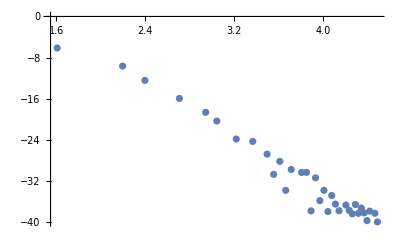

```mathematica
ListPlot[dataChanges]
```

```mathematica
line=Fit[dataChanges,{1, x},x]
```

17.5916344255688873475281711896497415843949635307166439451043041504308839045371397085085217819673312282457557902087739489778067316977678569074121332077409082217979278373861514211919203326913881224283908508444091177516953554102525203050512172132540745475866563597767500881410956616517870672434965853572685693077775730283024531738276781028292037848183098411793585656383135827700330200571806697030857693133600918142506274249333584240102909765022591166979974561593067308150143544419770417-12.9450988511554436665115519167080551372664268204494573318076771343134964610572003589584382408436738111813194148302748772481786324990116624783125277706041501528011432100912908701897928477344390610421805086825438488457147551085563923361272022289183771008123596587284847700353155223985530424720891658769090503102185869221283675194944609498286689999105875543907744696207915701570613441194249739844254970383250449888142896911511463824329582405379620160524804946840753806888769942427946355 x

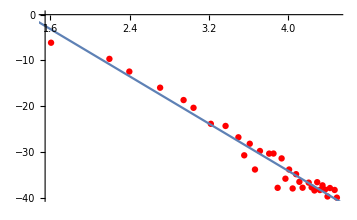

```mathematica
Show[ListPlot[dataChanges,PlotStyle->Red],Plot[{line,parabola},{x,0,5}]]
```

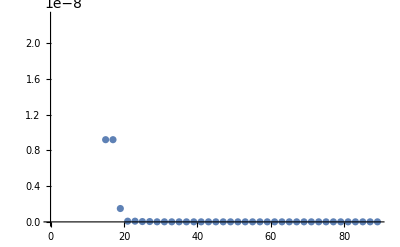

```mathematica
ListPlot[Transpose[{lmaxs,deltas}]]
```

```mathematica
data= Transpose[{lmaxs,bounds}]
```

{{3,1.151872038896995370187571057394491093205691239691934950686112774760855306889567752881784081488169195236619086983588865503254117420093160869011455645076599324013638448612151299852854861373490755669562399439288964411538401129895334181092099629240825440073581777938771853180822222233281250819010921715649569456842843482468554035188636909193881305607746977222488784402401675174758407858986505332521012401132002084281530859699926456804109640367881453525719219703134366435510565706643208372258372933530178},{5,1.1540299131297621548314974915851539312663473136534969521889895153779397202983969163678158465453452354146415610968688489901854560095025989681271214390075680070475262737656593701694981398128788151063356408898979780851155992715408934768488728560812784638091126442698001543620926048300454167636764643758510477648836459782659719823417613473719452116020091042095289442523021140930319017379126995275244981663594145079145015602139941830396115749314097720324070914426677813734999042756726254152251094892209975},{7,1.1540299131297621548314974915851539312663473136534969521889896094136887737583139068897112408457573520589336074731458429571194160923740240764073642723619749558572137082682365593909460087599817015196644639984796925518277117198060983749792295762958084100524117672082959839402540381156115293405105844370815908425508456995110336924035053895229564963394924250849345240202526477336519924924926140169678653938597370912976488326930205061130448164236578900666814519869907187126782155108265185794970927532401722},{9,1.1540928962920960856193491532397031645984876352056836960627776201096717361717735710648382975477752587210114933763434098155964329941764106937776973676827622974888490966960333896638787773317390725625840545262935354114304003553269650498030489410716869146234503139829468466452440731766689866473261541950142156343611882943929607931678317185700578969234051449065755871851755679326981104679787931885372417229796076498694999106781010200647064191201540000764165773391610156256663123270888311022243155623803138},{11,1.1540968196480896952137391471442681338133928708485496592083057456701108979945402077837235424902275814270080267826242992094193415259380705867720001296310083089053810934909964126470165120873000710258911068614226316391219720485553780149581736645895202631513796173688566373085694457120657317597881644442923298465751337501834165755143471512492616969065085628912524960605864882303216201548274040487618734450125869258724620170572166095729950759496678199204020418052535764255695526126634538723207521527308603},{13,1.1540968196480896952137391471442681338133928708485496592083055173072357346935342669565572058148132804341924126830766386737214346196535317556433687162235745084134860330191386627952242920089392835262530838099989215263035991585647511726969326109295408482313810628641125709056002793885522500661836596430730509992811462812794561481212123364186696420559964620874196147410789182916719442690959636667635626028079057446147106347364367599960678773987514723374204691130041553703941490208364676991536560911574863},{15,1.1540969351181001293814081394681830978396431359423413657669267248269781595295452753270389773635459185896094330585824940919370531175923658703930650885774558369132234729048649125940724433327714268206114964188531989953765188806033805214333992365322045668810563848184958401836356355791084327312057757234722208287761641499301533285127062022483182212090563106611430020891680556108402349003510578488965081400814459790171470890302831507210561977675603488358294585504419293846338773434268556149353571653816508},{17,1.1540969351181001293814081394681830978396431359423413657669270205953873412735832747260537626573846756491589104139694143165765504141591089997304864306580769290328750406688768961293142742979477422566578343741992944205256481443916564846208404475973462734259247033543734387808057936222301213902504312193710039790401209292537978212744640567348851281143853223605054074349174329685960001345203538522039501757272159443669135791038699189475914580124651579765256985506915937020748549264312858924880264271759336},{19,1.1540969428312073753381569524608301303370510718279453819377750461579323426677039677639187074832711661673944527340791032297273677626690562825299512078655914141784499558657271007702926854210856025247186256454519271503269542493566080014529582832797228598207881957258330396275375987941571427822230472492178127424863505405171213720006137415090565849336825932737484084958118611479695106730310722793992312124781642926915539853369563169908646280389660556708236234503086058819234071831471769300642421466231017},{21,1.1540969442498077403973294222906153952940544837138245657435803028033814163803994901230139583087886098097289063403103724807565911524181831221589432558492860277826846579220451183256791723306160780287830532984447352441698624361641122733271699621882523872667820207329903672300950990533321078893154152118562980210725199726635506515596003136147133222931132518404837744717079674710362549676978977987926729348622439730737685907218048594818948850416272254156578933429158303467588700999802453406963033223678467},{23,1.1540969442498077403973294222906153952940544837138245657435804811349357605891303550605918039733868626036155745968874024438681261030267239005386740330557183558712345133233430026926743672870303748251068511915711012364734691941842569004337839291523258401073973524807155910031772706051542229512725157513650274670501463297344771783175340629551726855968866910572953297487580686159484793516245995638765315439434011037190208598996130684537561940271420673322278574728765583796588086735384173644030716472065848},{25,1.1540969442924988250428047416365791502867103695433427980204438552677459439860124625156752609577982977442129842148796760620301223015267296088709399073362626326438496831104694809318676863558285301862073353344918589609317526264076300395793059437746972429797979190707925409666400566188714946800519617911493434744929612918894396645446212274296154962894334622230143217890971532120612802845438450077255629379857694428127602694548673527794597182037627477372408095827354656222757061924966474175361459192994564},{27,1.1540969442924988250428047416365791502867103695433427980204441711172162214672947491751005622880492070782491058496026655064086446514447375101425606955115510328918662763687773592761128719167618773923444640614276833405013129325710213753297892698494850641496908793504743015434249588457592330042474584191387236714732109525307394177741306597782748435538216205253914656860873108252831797587536278647761051752305509106225291210289015906991591922059890091403144508457104069486713835428549205226756378468437165},{29,1.1540969443193095979002822768603600966613925182699127277482606391292588673088525432194366020151563631757131590593124748946934393548249717568569027078101260782813162487559116762297209568466547953851656866042207429497398423046777433596759680529124152935105026434130730278112672717423458098552444193382824434724644683609791653341646314020899138658198647383588723427914794992260114637444578094691258138915461991468436858745473146676172341102482271724097395423317981405449415449420229490885975030192360247},{31,1.1540969443193095979002822768603600966613925182699127277482604551953626668674485080311477874531184455854422725802364055628087315883441874839674690878241784853971996091386254922722148885686460271629107298673632460953012816016269900115067446820703959711449107839783018798073551650677883168250017151457554445644919839522345865259953705224883118690581958966973998769602667588855116898347854467385229251876919296189335813937278205474872321608830125398723338735341209709853061564109102857034815772398934914},{33,1.1540969443215443986359326120059813947773337451114808159780202728165531386748075506844276659514864122295354365634506311849925497694193694634301665775507814176540540429222068921691256801844903640552207845796846282934295347703490694216722576264797704744573539837918447113581906058288120320213989886859541386654756419524872128151504859115676489557791130948813442825402322937579041453966614820478839895610719895997024098230866487880219653839555316532589586130096799874210056650700499051974202978765342109},{35,1.1540969443215877925940839179766300221087384497761094212950054390758372063790824070862069313135091345654614368674311408225388310206738904630766204220146143996358852905354438885192073179559364866285261939708848418918664115857598628518744414345371165147227109099823740197365418318115792179967009511957416518227821786491775345809138491806275635797518716527770956064715530852410562555283214197537097299097199896714075704709378401930013921251930045441209362219184259319537024276812910669918151561939870132},{37,1.1540969443221336345095061916040980754602678446050866178576180841185284948272213379953079298427900775095405483540485992398652693795849525533464707039753442864830310489133581996647372253479043788270181265544203910306375185569160638542068522995190691261400938187213370300858150488418154891632526589296153773856411028711837285584216609655123927980562395265923147111543103138230934230087894421917835687923783869959182660357756902555517694391735515477991720453594321251155981696261262195249553703934634284},{39,1.1540969443221355805087872231499256260588725068871483491487019470428736258396846470191098060433583335712300679722036163172358969978128048495591888195509776525500983387431896366309857951095884654075347920575559270405802435210671920977642589095265293130114472673607682798527466206662758617633025476218869615335647586742370180287388431661790806920371086927144257848422272915819014638847856348821460955011064193950125370933281800703620138156386188029784030193132084108702463752137352393638848924951735877},{41,1.1540969443222475223477632150817884154037111047821824557875794071966383850751898607602945485671830047127773110142799082443752292370876474145502096476926361324667359075958276201219528134154532144094808600056925073289037270751184698044854126722813082788610301462536093696982804537547954647265552909087186088506097680212812603411373954249685869504575346353178363429460510519457351668295243086996905277468263056291157529654837388353684482786145717983318464276001961593145387091225532840408108483462822212},{43,1.1540969443222475223477632150817884154037111047821824557875793862426785753745921746484623403482907299839390357237128559406182165823066747499558238242306320987046461816155120822635593267713367192219854167925423569038695971159012457665687697361059444691592615816050361918007258231810234425141154647947118020581029291531324722959369371803317669826775254112110403486447182920864866218052323417412396519704394002166620796627240029774871755876184242221659280344323892533708845533667206700262315604178473648},{45,1.1540969443223105339033776350494440375985541102398146106233757327683473450300157565112335162220647619452623877407929830608117476451518338140233940966209626569649262789053746318038171496575223894906387351539111941313178248353694025813034388401923716508089981548199799463553913646305011247565164690487166961868965033009522700874202798066597308769381652569159849012210617813365578068526883544763505475450723958973641973397191785864025559224322435763900656055377703609287494929535786409128363582645426845},{47,1.1540969443223745647003813311363856052824158366210403803376409498943078456785897155283152158634758604716601698335682382578531825783569402423092803941006489707331562377756851271036238193731946552824992130976952532740001165633317927332464683567987163146610467574966345638359651462196756616704486874537477730487104831073912382018949984997681774067450525409891707194368267039848710664319522981009937155507041789965007345786091769755830811361981161098116346471062707898331554783499915706161625779752200455},{49,1.1540969443223746001149199068590037766536684521484925925329226537684483770727775683945001781303661327696436568839811972605699328370459534966672124284330320437284525635921352559773487625561981203477027508868021125217908107812319039938028118011100662278126331867833185701240132478774229904490024410559509418182623664753897620358772874052235837558566520797526671258924297367293515097252439107467962679202598851444338513486052852349663172231665230425527908615758948933093948003252852121506382904396957627},{51,1.1540969443223967137004396459802450647385081680799898424894668829680491056250703506055929512199651480013013420606794546942677170047748334148415018245430361435574786192154092323188169537415689198475923385181731709249199671565551734619435839192973997944853050979163364354246438701719259747585805516417879612289847952915932646345077967196424943982401436928200577799294023003503565542955045758433306310270068588413182291885046192081694803621831351409472677397606473888801169316371560659580244347819995086},{53,1.1540969443223969747799972437076711881057912472940913189695526898499423371710518768952743007817977986381877559475999772497300326117359107873371775203705340540071388344138827500095260577443351627501624664295879908828107746359157905114933019656588251478740502373762765891772319752174221999724894104326481684747855084754448332708741183188862713559879912179048415600963016311413301417253077153611424738954542123303917609400150270500200783518530665458091644644236203594413732969129856567444619418642833319},{55,1.1540969443223989162731583940798417172432584307035645887888991558886206911102010319237713505377764310696717334392071312755034568867488660299390920946546107310545279385047103040399591026559648770433782183073673735650989526074151982552994734860772826867699689416513038956252700552865915687288709394565239144352115357146769437054725722461227784368348306406568705595680430910998171930744006151517533403957282458521663477415025618213488579720317921217904242457738098855809416697356733188295482768910377379},{57,1.1540969443223989471326215415327752016270069696925922803276385785438684561941706602167644775511915570731622814938758588002766896883109554111250022950984146955088157008478623481892991050825296161926545700055908582374258706281768770835975583042167552293968104964528313606608850591440861277658667237516033936414786480731320631217886597508858138798260651961134861625915446009859506063590955013876617401726487543478984634606563756510161429394486632986137049386892185276466089390547396444534084216538625098},{59,1.1540969443223996483485218882011782785582703587891721775636230149766291098043339718373981081514720287065912919402493491982349171141056356045128316136266687961116141566349024912981539731172846187118639698233243199004957037724735773418382519675457610808275532769484255588846601986489331426106625287602272137425644181259147597879169718484089975292846299694030004905079839229111498226549797675331943815989843020247014101912726317166901296578067443238553404938651774563222633808646812902662561562954831676},{61,1.154096944322399780378521118301448519706639421530206910336034801145807664734868184554938710543758436067616493825640888321269724982649913973151838118812664021569057033571995780513839889552231541185475087301486945759237752463179425146463026565756530755263782470368937616631980916896048978085161996011590253101527710053419067039897477278465919767861853732943028603095297968380935005680514599131681602380328383448251697124040716649267495901006401440282543957021350983911749035317875379710100548539564539},{63,1.1540969443223998166785442838342230127733731882703082144102574316623416161831318425113004768794015346483620758993702760364063862984069992164205271593284376152650664543800582339293423820835332840078041740425836216715469321578533451730989485795984106686351981407248203287206558529568875495219664137346542352404527240293927426663320159206458906358654172414961327315529431844747970453892843386800345094271234367220449911374646155764455922726064410242635264500944114737070297591538470696956024597331861932},{65,1.1540969443223998166785442838342230127733731882703082144102573942758470017107563816161419929898884295721473638219018869020918625878029068545319172008757773837483667819009306580374798131497892646907598429058250125321827471939969263239509689453097956874202515783703437213576789335793360414376792391570701800026742480882354338851145729523919965312411421789587104579824310042671718128749488433107987200619021097352422892032044852821139278524962055545727242168514930833073572478168654875784626574324434883},{67,1.1540969443223999269722220618702905271238563556813497074425115328912169365996356045355361871792725157095373298952166239369253138599963625788729200428385246751515215759823151047410504976979828935206876180495457413980265018500681935915277322280124673977281661811608453704085401969817479287622814403968696128777776513548513059736464075299487067900284263087721111557837562195637112593136668238718916874686517562464906542632545173978125028534982731427447621936790194791708061112438776419291710310678412109},{69,1.1540969443223999664219704654045087561234864788095384421891655197193541728885823580103105790380878594522864134685762829826979728511530025350430890967386851892133180614193197997523138094793076036428446429335335982008696653077173979070337827707318468774700681716637284571577805383634980187378075829908934152798915474716790858704000126907851825475240148167764563469559719755920797965399006022451089150255792895199612669916054198065028455592219080094908553346550416136766506019743981981600068625195710179},{71,1.1540969443223999863554297245647570873331022124503737270611005252050622538027077132737214550695496005121755936478674536607592484739112725279114279378805958090191472499183314934042073188968105387056533159478427041082071916427260451648991616236648416870001572416523389208588802726452794363116329121806258854690364515541484674784779111624699254600267852517374358766308614585406386729909793063044588293601007570037817986864200448735355647610184422705478748544888563386707257621668686776387192137393539165},{73,1.1540969443224001082456440507467865625168265353423676165182275312441924764813444954593170452021392395954125506236620108194954949810325865493481105662119686353826760790845055421414817468641958205220338418422570897016060359027623401133616930131581709549278357465438873999418427699950086044846165897364987003716338455341522268923471933506137540420503320122531147832606770753653568616841359576013069069710220080605756127806448089933589946640361538373094882173868192020836130284710221476172121439206761423},{75,1.1540969443224001301321183563925349388544854845958271554731462411222242818446191077079982677392833305520014880494516464159389910493695866334293954461733850318678071137687353839904399690242820590353037787979184532093515673760776757934021648855450030051091425323825781604897664824831833915392329591948800521498986666909154264872218326725247569221452978119902639782117676605494605148983210188836237978682615041756092999691413205154599722709685432299662959054905236081241111335959784918227680183161243472},{77,1.1540969443224001909751706444847534531781147663797933484445942870617316681341248612645655741478042432045822606098498310633490493522741225169702182759083612717715489985879948017366673379488707492455857670539150861963575472607636743163953328437868139772037748858297430619827094018391785380376782177378164043657320594487043862496228503352766850176292642658126470483899429406910019811224715269368898390240694816854435112404986514247540746037522071875988020360238193694352354647351811282737887226164471078},{79,1.1540969443224002149671936794432144945155243910898162211991434629583627290724982637819451383487880237929739270574285647393404346181165145631975889287464837994019125976381508128652076922591286324195047978123736637566312981011969473471710964671537916076221152812839666378688085139470406730644914496139801622837976606346637863459742569249628821010873116189037454977911837445899579302098536276194402662781593078867112890622168501633217867124586098383271967225216276450512271884070976080591128705668476704},{81,1.1540969443224002203055375646556037712742901479839088764079141025679369524520583646551340863648049420889781072726315125890175097155962253120714670571106519365248184335269065030759667534268746680415941239417473179219261947278933887645369199305198298631964342585883331245431552561190086147331551687040541352141738446507852571076867527978613946056866423732550623093541006085597860619695610849727052856684116507265861760674834432287712861385154572491863311333932097204144013435696970557629254180905604694},{83,1.1540969443224002541374679290330925154823071086826427371609783770771671540715590337769299254254051804329324234858312267357865624708014522607687855834244037130969072709210581155296999997322969646957820101796973762165951126766586321310471945500962796298729100235677111945912897263784654089749731073541377686361881809989621799002626436034384221800463809526109328703745189304848904658367247477672631412198086615587980585188681002053873056890132908642671024027786924864403835852952346646581720177138863656},{85,1.1540969443224002541374679290330925154823071086826427371609783770771762093281916221410102225044380962560585217359763406777462148982020304559226032540151862419030895581883508327796248860834613293959392921739167817340754558228127167553022883362528349049359055251475184432961938954017505304196487296018571955826256519122638958467458439433663673468663463433646922718242243569097858489032196308561611602941279499205708629984962689238161950997519450635743269867512140371475492833649380603334891052177085202},{87,1.1540969443224002763341672906101040583403813317451324350132178379863764084097538065185576103264778515564580412138188527131393704042122210469576879484099571510155142780394887150848453430497709611242486647446391316227703720041128411607968474369130241306998140062213154971252469491439684762886039035896605341887256473356609527507811505417578018011739384951376623689260708533502322455131169201873729840227172469544243187212722443863519031308148162994825811851070301900027953207397404821741087917959026164},{89,1.1540969443224002804759638473450086221252278285633342003186162317931753901392189863712460524763034965061229139776568841083874522127106326713306973193825059127247452525694878280464190128427457827687373638022992048487441382359351393567375484177988640760269153074057673899040317405145914565847293148928763416012690173214571390958564428492148483213112504286288397384579042825021924009668455024826743946765043896689262979148663444901758979285973916777772423293716291507904731116028396265950586434551580202}}

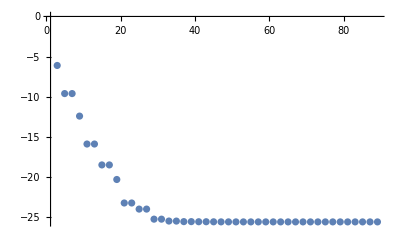

```mathematica
ListPlot[Transpose[{lmaxs,Log[deltas]}], PlotRange->All]
```

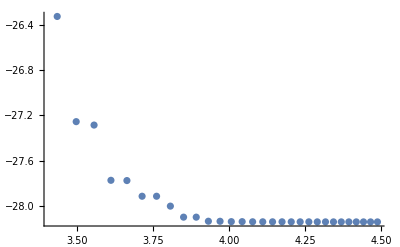

```mathematica
ListPlot[Transpose[{Log[lmaxs[[15;;]]],Log[deltas[[15;;]]-70*10^-13]}], PlotRange->All]
```

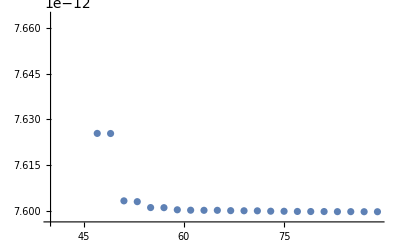

```mathematica
ListPlot[Transpose[{lmaxs[[20;;]],deltas[[20;;]]}]]
```

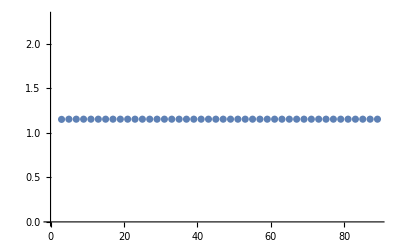

```mathematica
ListPlot[data]
```

```mathematica
Dimensions[data]
```

{44,2}

```mathematica
polynomial=FindFit[data[[-10;;]],a-b x^-c,{a,b, c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→1.1540969443224003098611381629297203424423594128994499690920890126395896981582091694058115333245344773038188040642590136005760625681569372094349219390334026779972382750397141875116584555362198526624733940440144456089345477952744412685530509328591567670293167509870543696185646043725098253759068322769411921199684378095380915627460726715615321031320614556834140527962207374709174102160010634130254851530156745117744231322841125336255930402138340817742019432068955565024764218129239525145687316875918998,b→7725.5671636067664914719603488068110617553985742932973610181799746306920387119071946627656344731329287783134443786287533095909147500967699555671199216937343289218521792121912566573782398756819344412179979535316392343270949427480027039754898717468628021695792316887220630595414114459569767873166974149852314509400563476719961099019983539200434347095062258708215615833045241892645595086661041621626837386737291279050703223542366628533921142167710824106666987851209685234208521652579330221695371244184976,c→10.481872475863916084855184228874379638543489747836340180727515187171958839673453824085971165457097190846043582713371615879729208803117837539371310793072779552552007526398510185680570795676678680229713405370439532887587110041712486629195085149825633504072099675882953953006187876280018495787515735557597456230997629358944390482549961013442541219003357189235400151604247057227278376373208867812790895056076602944600469392212942191603328047016482077393242221858464227066881920792337290698047963501685909}

```mathematica
transformedData = Transpose[{Log[lmaxs],Log[(a/.polynomial)-bounds]}]
```

```mathematica
transformedData //MatrixForm
```

(Log[3] | -6.1080408697032973289668245157255275918875402279677222154354728708028851964986574267833141223821945315347956950981469735230960441778864969136857866029012562951439564927532504719810982695710151141915677700153789217080584479649136500978554932715002794619071447479289012300755788561355831303244442762619835454316557639106604325889516251810647007289859628600741706398645489895060709897273760743698347032430448887155746137055601066829939742432033725076735059663855844199156530147129334131962089908885034
Log[5] | -9.610352485150053211055739937399461942219024122468140361453729594853044892878020006507196832964730846159085888133144240271584190123669310963828925604303456177062005767240421138450270789490497940755560739545686024831526961428435284788276705227401513838908662390419447809978272727417857551052327542142065834083662894499148567852166416231050198492551680464129306523763835335217416123028362989967903466270645212129076678737072877300364070253361641135839990001917481899401125762377962240158498524615795
Log[7] | -9.610352485150053211055739937399461942219024122468140361455132460375087440296684203437335200321769863829523768926976357710143849272720534335578386353833745164557358119392291129285961666263190861881022602761702112026831987464086242641829934988936436247614297242860750652556977272865966350918475300825325293374617452237131140741650683577492035801323613869283132570082545296350844783541086242990096809099250075779186946945023885482504209834006913201880786351892126034417884262314362003815582537990472
Log[9] | -12.4172801397857276952212257480816476737011252519430594765077637568729303435520466354652022736959360951860972202066285723931412809196057299099784359131885350881396697545630492350282531817306211568423307335208396210607268820514057455811806780564503139657669663007494578274174945723822817620507989742575833575385502270726715430582037414569561756531981749319789308275847269595809079097275143229825192029184047312506512056741991237220449148100304312958008438544156006477976245250013798679719492971362
Log[11] | -15.89756101498892771806796112867665605624248697095077266402427840801349591638486572346744741669437332043723912274164352176536007413728669951199583255290675733066500625756321667694639183206439682017648809474422058693272970943680143170088809026696366022739962488590137785146505484848273956256004102028428986686565472903260974428365143216628994073716267279079272715548530455495980008958859458576082848813096669194544648819491283179882448644448605063413803146525459996038150008469599225070337626793
Log[13] | -15.8975610149889277180679611286766560562424869709507726621926029486709381030319790627991372962177551728239695072284101331196316399912986724621006415498732127823510716448243247144078507892032341204553797162501813381739085202247778719255148690690200288474907378725532607235576831172037009885854507994278676994294155259352418475874615639417141060016424392741525892548181693678232658814271996529542651167248638089933952861068169836355665593299702767989276191442995023899850402418016981667855353859
Log[15] | -18.5035950511721646562740907299776929168999219214114977883321701381859324138384823423424933785178609022020913493458809372707989350047379656475737480577300171029172159635758881820833194274336199061760165087251780359009884335530071220902977685785560636953275240232240953005053016564452788882166881985461623026466091006373537393661071303295501255327153072277930415256929872426593039542631342107430188787896855347662457486009266446631627932718676700982572657116879583530533038849325414501436991952
Log[17] | -18.5035950511721646562740907299776929168999219214114978204658906147304650500263458259118588627700737727143728540202447426265917084540562541434889578776760163889624476727503664331813309326660324703591085584888745365670227831961130627503750355511100842580628844866289092173132839340291665035283947330730119287038565099798456528595300031072315392517449930022000040233145576990688422780495901644903408673131754308122329617952807783212187748547118746797156139232162989142120706533146602134268687604
Log[19] | -20.3236894101233999599417280392088468043221532509313144136716496553844070868464756720679107583067715289034201125162657157876487310161687052147591523078627858423517179340225537441106463090254638511798895188533191050171209676856506749662086652101244925799276010105877214593046503030099396656669214888304203989862249715374601139455987372170466519707847181108199004168663711075434282853138938806181938908032832821569615708234727755046445593563849705917962899211912188683078960616545752605482695838
Log[21] | -23.34615854831916308635329993519768231161109961585452018526692959587529777100278269814674718050000375283726607695987112333126339947513605167489240215349200422165146785536532266936591713529337927911198759756545596970122084878268475864925049921283093032008719474548339659187693643554163407467273916751028648152492297376713053457225811092718515419513861809756584899625166388012064673038682217537562098174553477343560286935076713853698349510755935512793261196526442903847341102189611522782347988
Log[23] | -23.34615854831916308635329993519768231161109961585452264187585887639211117322647533100362704711694897427529996310779779820261226455826746609186596113816825628759223406921369520572861157503587942107056808663854147658870236293909542630277306316372526270298441392849300393944087226747923644248486904610406821471495552454697407360700110766875174883564377001363011265156063971905408628029727010018460489435186842025168316749459379575254772304378126597392225199818991078701317802383607561435977332
Log[25] | -24.2331129772888642687847978953127562544764169428192779635406678577907605827128335005898621893361310321458394349973572401135754902888374321096382569674720514243106439136325460265361865062163871728208410403932835080815438473686616407718274491771233689106151291902670347025703149051895722621222406063025135046048662158429648867187550770443131426197752263798022792251194610441791091110783147740686733240208236275532946362944193951893022550975587259899217065652885169774997892442975710717920086
Log[27] | -24.23311297728886426878479789531275625447641694281928852654354869885522677056244561293705064487233988186127418494637865290114548233336368940716368644485987701142688551433854530899668414871563686931589710418730444702032427140966977558203291009112092358911277096817746573348699676090493431652454279519104941939330562815101964647047640743591960574307514935964731735359421292581153586256757092816742065528942732857631961529568571761368816208326263665442599022636369998295831745564150353697904999
Log[29] | -26.5026196435147748182416227112162053534348906319806909184194621987439899190175521222137656579743855753163395333957747839366554727469178536785009311653039981517788932656831355478307754006910131829609318007667809940283065771185682899383563402569917500965083734113618494288399241537639700960222187932163508256534644527426444200642019543981718658344767244194994798266102522923094617732912571982083254947642392319383977162119655305036816536865068800815051470228055736569411502195501709601287783
Log[31] | -26.502619643514774818241622711216205353434890631980631406598713459005171268988867278554029691536927732076870802264300484188528869837058137574914502052383049009905902158629285018339360489287925365493767851533570405383153571652326446612708609239988807387338104698887927012105082271370756932582661807172388219833837711183816109266127246976736378911830605543107086281817512708204137674247804261216783241350043561319105288831305603252764822455530531496742030542202141506689841326085085415546221
Log[33] | -27.7866097330191000189974837841124365606533264013861688365979096472688814127706853421030630376819591640538998517792388840677832478407987130139833893962539038485770254426452943078757018283227729584565485822543328749423169220242398176110472013476165582076367661055603392929928802080430103600053072656001616909999031908022251336745013439106154255912125671940286639966013440948327761390112705231560106459384486188320932976007687458136105912093442395046237156283311071559145631005321638123695792
Log[35] | -27.83863922917353743082423252735054040349782637986383910398905487482498908177267272221021829618434766533691520588010800549503330195711857520005103480837161922304791700225614224071139657748754383505121218079948891567494697650269538330470536661305935336615651920812332168835631839053324918778685613900108114423302542101873720422660249950058801096807656555293161952047282534401269091146484127865936810435901943998794616723518377363970111445585314477601112353432865735260628484048012777845239
Log[37] | -28.952744387821321170084105063567235773174185399635098776843655531465989120235053176596333580326280240001125504965623600295682128270888550331463814889614219654852027497016685237634634607489907492168624292792221713419548798292350786492475010955187891933765921599406211807114278661270278519950029895011391311142971490364439286196311972679950690105976654934205256000912260269554744621160105145937821898182826986100402267265403453573022358598052975087439463975852099350671240477692197482617409
Log[39] | -28.960068402702065460247392573052748819391355378373646176296690839563353367169391320963080540903559385163504996920898002640237430705709486993164012597443800877740901413021551454192198190868330732855537054053442508240937718266809495016617888229801704698722831203310831324390504910306694240081330739754248882154150176769087195769235784666998539073116641133083495593008267467383125437012292601764736111447258107511765291910653267542575174897978909017774435134780873595428533576944776470672637
Log[41] | -29.50972824026776544704388913850992306203964165152313000828475597267309194140794781871009721029584257873849580488777090194868077236761577996581675903165509713805809826229147402959641889848090210275382835896957913583870872560545749957084454427363743629799401596896168083504883958019575521928852320189115243180476305630090437109094562106973298602725726143869003852785792413051707374954622542361183188275392975333245413645330242422279456616104433046964403745099203146466069324502634783963094
Log[43] | -29.509728240267765447043889138509923062039641651522992863832654847232853958091860899285188298826940668736291122341555685250661549513944498742284014372220877801701214797616544782771776387925987012879364363453754191227649044549304128494040747150909813261815842006591648044481311481201206257106942156515226938084208299336244382592164197123028339172701237060150404266430832147240639055310415279749670140000335725018146620533877027672898467068252032333915564318461844571158768853576081025143429
Log[45] | -30.04145918640066621843387744115508386133408431447239017787892544559775187584404523428901210674213210487478381025603796126906943517377033557304926161245548447898471577355774505506446226083032963871951717805726637209777254094988980018754173587646779590089285085644384368082838525441251011917210224560589296471164457722968544699504033034811967708880451859303974988049554747247804244734725092438341738899261003094100623337827272713153316094535998150491340629427580247141173316693077732077427
Log[47] | -31.29052971723585123898924666567167694263959784306883751681510748225740817622471093526679341829321045103110307783615660221240893055425468521338848450354850208671792211865128543712144606174963403971031154912057684965063096982925988294156163244095746133854246729101965268415886632612552688314561644945155588918990477305960226089401310449339685443425950404410694456852509888716199989846001425203940698976331660496020766816579852153043961538919530323376770890242209777026778400841340646040972
Log[49] | -31.29190624461680270955675274324802885616269677048756441582973815278329809338223852613427296113499002811644305710822363064060216639521467032147964694074132297880086796307408332582041883008458809312222610596365217407080214152190716954901906369045135341803118787407500744937554974941254719117730739815534341919747897781725693964351039099209892865271071218590758318848122228864575653583937941864336410339762265036619932216169308598558473262513893310391320910394865051622758676496627405081699
Log[51] | -33.2589095911693875316296477495960303178850928998292551056309389288029942864513768246527007286492680430068242115367030990323314860754109582042944795342933605783497106380982396665582487206294268246866448242283144903093680122781596948533272706765876431710323395368186218265846895405436665100995453402078662768078802004924064001525741786837694828396301322598960180567444724660581804647096069890124392542464095548567094156721545452578093880714122305503349209828605275854275393432794922242121
Log[53] | -33.3342793857283593035438682477730895637819066697104415109476360724398189333435030240802608295553837998292219131187459957011151115503682602055028785642786974126312753081059523782005640057273354351556805087205058476852257594542287018359378903155165736763674133843725683159253465928432899107088587175123654926648632293015130279622799921285100209484398711340113906310113913055491528882530411192137423378850431906052977681830835242084972637942599518340006332926575322064088630694734546082449
Log[55] | -34.2068946931411608327102374945022038193180340958727967627535326544595253908221384561542107395915296508454621253055857586493767195860680869253274588818608893474161995184894111702280499675206525700360560351155583178016789829812317285657466939913199165911954680482574459737585299463309523522267048327757272383631399638945775049603095849087867105120505527023228764716369696299075144999977828128005953971542100196593039472815834131251398294517219289381626889628322285431079091884995843975773
Log[57] | -34.2292874427974099373037146886718142162563922682673199182094918870168431940782196404362086142614683763073721582720430755108237572312304824736902130345664040389690166459363814034613857288277235535127743520921502693533308296337005556755462526769423954163983677145048249764557786475090995776749129842361995025123009735323856580305565258124538288294132021342742037018018104778570508319103460560445386571166456725894461979645123200223941690740569378886574030038016240022288357154154510092445
Log[59] | -34.952002618297872592321518499455893134058531344576887795421615824527851789746211556767046267937899348688866769541463569511347327292814244270628896215522909915254582662090764950691922280420187487397633274577985151750106542865141235007181097472581808163261212095531415510814870798482502675215721867234528516392311689890147443585495794558450084091793613241834179294777991757826678726377348039307819192352850190475596853034829829375688271504214745045447346933189497614114971593685688817964
Log[61] | -35.174631338390002318686093295278266528110863931685568369007422407289410385823247260437178336377991805941787410328775022894050525558895050970158251817001672253430424934647923485851049409059698542921891601464741080047912007472413761137171308392839519762728782090803279574290059199736468038295963954086138805312878778103476555854485838589733533589746754900773607266430810230691644238300251526046872201287290126281311043368122932710668001691321209818840504106907042542617146350631460311762
Log[63] | -35.245652195441363854763905755646320025349082122189985180837673093659005942233749365104402165881387684318525532514647876225693131457939427917306083157662006828809949664069792754372371315414761120425041144468205875385711367952818343084223026831462085952637575839250601971872870836308847318862355136795919018935628605518037317735472999676927411807761205245084323151716499828287286792822193355901278989970173662437515836494314621570545065458707206916890509874726917699612998333362735219079
Log[65] | -35.245652195441363854763905755646320025349082122114178582878869757452387900023452226860581366654076136516036129296434008677738191047753467225947879405387381646421760124153855588726399762395293085117416233216424936152003052993028591468286312929475457930299888880028751682483843170777804709276440321216825199629571023577909690532994267346504632041632460057442107384706693229620910666810655970723762501179737215683436896461277105359775786599587071768271957897209752471648079559406623083285
Log[67] | -35.498786763070497534451760883300773434261831610444204410609461770234644912406467215218261562066942084146293398510806184846238813167479899814299989165993375451554422829548216474350068590120980574756582154575857823747623349307527344564133901836455072647641097372367961426864499526630809771738724238090910594535336015478241851643294000270186620113297245796375999722022958793271202506029826524056942634361465538611855340317484167558363471357578962464968351313334293830425089085987730627611
Log[69] | -35.607521673408509066671062672183316434726505830270931559964360511566046145878326622582149192460543781692418201560956818802828109475024036890350883128546680596571009720496386919468326653071232809983307584187851404473901335351734898467246317853884126356633847206627502956805254492097845392010557574746882196571697902635932876173307715420184944580258340267789132630003938512190737571690697742531235638529820612710572658903209891101143223024771259981956274199306040280410411077646036701672
Log[71] | -35.667314914239346561843917207894662140038826750246276520837158267182009234912407029607598286619572745398470410117952378413959799387981844900780196588614231790676633487645377710552229768988861423299260748756808347336017539936223805342351405551381721701303982846872111495979582130520204217713562956054412946249401913347434381262648512674330391306290455513998820082846367424131413786787433239174877146606808252151332801400985673123347364063815464926887339838110098890119770369754384859285
Log[73] | -36.140169284933664801292760159056254414697909787761098790288120999345932414576685867715750736453379095040194253553283637494918906967476772616486569285559806272155249553696169227447288624928409684294610726658212288982919375493251396577688701737185335279238886019065817701687940114109834861007986664173841559666609608179524965274824660518425361904868485912393213770554248524028693152054978792628149868776096146698775289367369299867823052333659854393846104667001081318052865221016164509943
Log[75] | -36.255081402843538096684277067049678573931407258541302755426833830175255433867459546153187842548946855814351173274822074929280817334672512643176546287675421807179493275810843821390868241860631766449113883434048965556398777883746121702178701060637071937894929438028251985236139114525108080694513460982069295264005092275970780005235946514840231504877121119155781442226329390054203711983044123456981242506675611266564446346477715122576404887226023338977494392917116237016299007922467494536
Log[77] | -36.66836689634975508766894121216140112437551394285085851123120340455217709000711358642907773545092691595990038960222007421150872123389985413129773779872110885590350095486631935812422422470201922543774574840251852050958085320816170220392035508131902289684584928809124320606737355020975710684472808062839197931337457440216909494869649129935312619261549334019705101974303600218502537833259056029274447269006524908705400336044313304738340075270254815054783811679724660715161791491306787844
Log[79] | -36.893771779759777781142275186475110117028094507141452991237742831749571140454705465681829277653131545290701597425446595643743166657729088217446735673573548336385345729548474331253599351440253859755478586620340319679384082528043341233870545680992287860408067921639207017118479537676358853224404709729164120390770289156953099699856623479779379449407124723415252691009018514685215217887832817308700800183158403972828275360375495283669830340883664371859168599467263709102927974934835850612
Log[81] | -36.951672005764144044639921353873311046308264132094887050078688245310927136877498760303169833623024419452109347736936688246869226673925815489657058470522140809622916717616572642715128965528075330273837836703462817518281076719527122404121154576746954608787406132690262944423739958193553795634573705973318410332462079221696040817034640005182144560586382596444640608024973556863007470102458047914265233604156530705268818028828783872351315536409229531319747485842949590809151699489652920085
Log[83] | -37.4261266579133031094795199132633085589955907911514178620943659159480595320381855722056044524506848531829978135730946076967280775540070159982442056582546104639420035870872399592811594523378651485505777855775140803092351920662812976945698457546471174543484168051019442204631725090986955947444144130437491108605529083082886079218605595578333645290928952762130924561372305338688361854543702210390795743871314164826316927333760061076869191376664884470166410648699425117724099260502902173
Log[85] | -37.42612665791330310947951991326330855899559079115141802459724116769457132367731932031997997877193326468045548986699528649269927011437394155584532748502889952445772289656782838028711375355940235730796762182544208617220081693620737306636786248575325539475060429257356319902839065504123232534855059307822381429643859550966654435734983595806100011066405132580420969168383292246568388789471105028592257350627439284741038738489737774068556660245163510955265813847705601372475513668882048948
Log[87] | -37.9341814583152387817304611012040294306683298366990178777363322920492982280757822678195464291516641239740548498501846742607552696041969583011050610837950727536075574204419329898566826808612876192556871615819169700317767700923167137586595182459065289108503141085405077248696603791536952161374925878608781025434465834382006393737827806278303624938648928146418869660916838090878223937110868503545097927120728295074386189053834332315235554801459400469084880650780614341186278906446954624
Log[89] | -38.06604140171768676322183734614142022775368363984204778003409550207085231476588109157989532410063081019678274947189099581644495798429820434060314407979280247169792377232415503042826931065277048606875831261956317233977478728543975533130039255121664914811629192710589122464759522174561619698637063005551109327019587995895969937271857712434800369075374873045154517284829163579311935973174071925335186655505244638812662143814769832656930051523582084399160874137639375397913870186202303546)

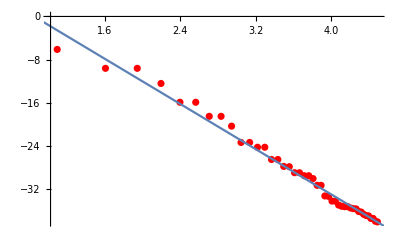

```mathematica
Show[ListPlot[transformedData,PlotStyle->Red], Plot[(Log[b]-c x)/.polynomial, {x, 0, 5}]]
```

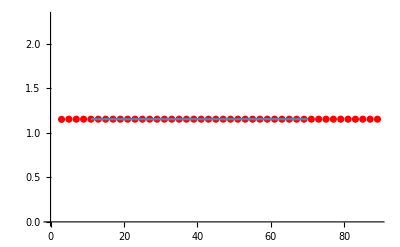

```mathematica
Show[ListPlot[data,PlotStyle->Red], Plot[(a-b x^(-c))/.polynomial, {x, 0, 70}]]
```